# Season-specific dominance broadly stabilizes polymorphism under symmetric and asymmetric multivoltinism

## Potential for seasonally balanced polymorphism

### Conditions for protected polymorphism (m = n)

The region of parameters consistent with overdominance in geometric mean fitness is given below, assuming equal generations per season (m = n):

```mathematica
region=Reduce[(1-h1 s1) (1-h2 s2)>(1-s1)>(1-s2)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=s2&&0<=s2<=1,{s1,s2,h1,h2}]
```

0<s1<1&&s1<s2≤1&&0≤h1<1&&0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)

Note that the rightmost term above is h_(2,max) from the article. Equivalently, this region can be expressed in the following form (which features h_(1,max)):

```mathematica
Reduce[(1-h1 s1) (1-h2 s2)>(1-s1)>(1-s2)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1,{s1,s2,h2,h1}]
```

0<s1<1&&s1<s2≤1&&0≤h2<s1/s2&&0≤h1<(-s1+h2 s2)/(-s1+h2 s1 s2)

Equality of selection coefficients falls under the  conditions already deduced.

```mathematica
Reduce[(1-h1 s1) (1-h2 s2)>(1-s1)==(1-s2)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1,{s1,s2,h2,h1}]
```

0<s1≤1&&s2==s1&&0≤h2<1&&0≤h1<(-s1+h2 s2)/(-s1+h2 s1 s2)

```mathematica
Reduce[(1-h1 s1) (1-h2 s2)>(1-s1)==(1-s2)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1,{s1,s2,h1,h2}]
```

(0<s1<1&&s2==s1&&((h1==0&&0≤h2<1)||(0<h1<1&&0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2))))||(s1==1&&s2==1&&0≤h1<1&&0≤h2<1)

Assigning the maximal bounds to a variable:

```mathematica
h2maxForm=(-s1+h1 s1)/(-s2+h1 s1 s2);
```

```mathematica
h1maxForm=(-s1+h2 s2)/(-s1+h2 s1 s2);
```

The conditions on dominance in the first two outputs correspond to region P from the article.

### Figure 1

Three examples of the P region are given below:

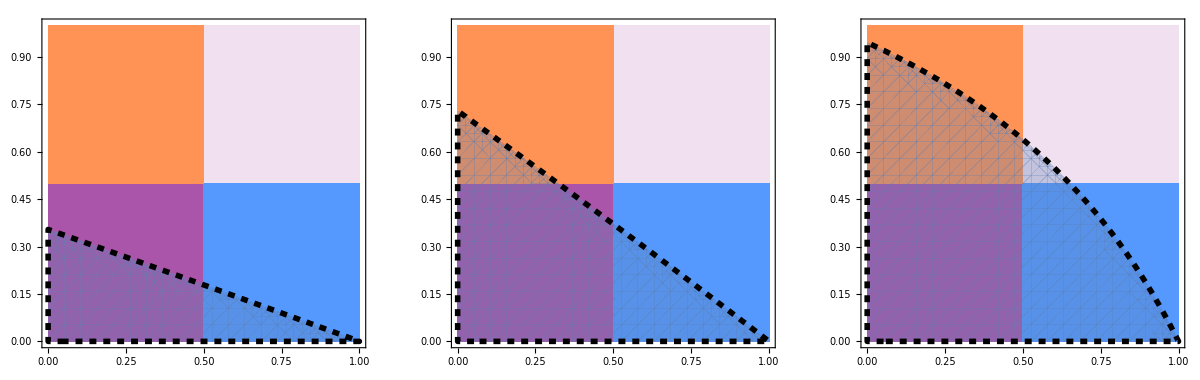

```mathematica
GraphicsGrid[{{Show[RegionPlot[0≤h2<1/2&&0≤h1<1/2,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple],BoundaryStyle->None],RegionPlot[1/2<h2<1&&1/2<h1<1,{h1,0,1},{h2,0,1},PlotStyle->LightPurple,BoundaryStyle->None],RegionPlot[0≤h2<1/2&&1/2<h1<1,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Hue[0.6]],BoundaryStyle->None],RegionPlot[1/2<h2<1&&0<h1<1/2,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Hue[0.06]],BoundaryStyle->None],RegionPlot[0≤h1<1&&0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)/.{s1->0.017,s2->0.048},{h1, 0,1}, {h2, 0, 1}, BoundaryStyle->Directive[Dashed, Thickness[0.01], Black]], Frame->True, FrameTicksStyle->14], Show[RegionPlot[0≤h2<1/2&&0≤h1<1/2,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple],BoundaryStyle->None],RegionPlot[1/2<h2<1&&1/2<h1<1,{h1,0,1},{h2,0,1},PlotStyle->LightPurple,BoundaryStyle->None],RegionPlot[0≤h2<1/2&&1/2<h1<1,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Hue[0.6]],BoundaryStyle->None],RegionPlot[1/2<h2<1&&0<h1<1/2,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Hue[0.06]],BoundaryStyle->None],RegionPlot[0≤h1<1&&0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)/.{s1->0.035,s2->0.048},{h1, 0,1}, {h2, 0, 1}, BoundaryStyle->Directive[Dashed, Thickness[0.01], Black]], Frame->True, FrameTicksStyle->14],Show[RegionPlot[0≤h2<1/2&&0≤h1<1/2,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Purple],BoundaryStyle->None],RegionPlot[1/2<h2<1&&1/2<h1<1,{h1,0,1},{h2,0,1},PlotStyle->LightPurple,BoundaryStyle->None],RegionPlot[0≤h2<1/2&&1/2<h1<1,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Hue[0.6]],BoundaryStyle->None],RegionPlot[1/2<h2<1&&0<h1<1/2,{h1,0,1},{h2,0,1},PlotStyle->Lighter[Hue[0.06]],BoundaryStyle->None],RegionPlot[0≤h2<s1/s2&&0≤h1<(-s1+h2 s2)/(-s1+h2 s1 s2)/.{s1->0.52,s2->0.55},{h1, 0,1}, {h2, 0, 1}, BoundaryStyle->Directive[Dashed, Thickness[0.01], Black]], Frame->True, FrameTicksStyle->14]}}]
```

### Area formulas

#### Total area of P

The total area is derived by integrating h_(2,max) across the permissible range of h_1 parameter values.

```mathematica
areaTotal=Assuming[0<s1<=1&&s1<s2≤1,Integrate[h2maxForm,{h1,0,1}]]
```

(s1-(-1+s1) Log[1-s1])/(s1 s2)

Alternative derivation of the total area:

```mathematica
areaTotal=Assuming[0<s1<=1&&s1<s2≤1,Integrate[h1maxForm,{h2,0,s1/s2}]]
```

(s1-(-1+s1) Log[1-s1])/(s1 s2)

#### Quadrant-specific areas

The distribution of P across the quadrants of the unit square is derived by cases. For the quadrant-specific areas relative to the size of P, I divide the absolute quadrant-specific areas by the total area of P.

Cases i-iii are distinguished by whether P intersects 2, 3, or 4 quadrants, respectively. Case i (2-quadrant intersection) is operative whenever the ratio of selection coefficients (s_1/s_2) is less than one-half. Under this value, the region P has an h_2-intercept below one-half, and so only the bottom two quadrants will be intersected by the convex monotonically decreasing functions h_(1,max) and h_(2,max) that delimit the maximal bounds. Case iii (4-quadrant intersection) occurs whenever geometric mean overdominance (for m = n) is instantiated AND both h_1 and h_2 are greater than one-half. This can be obtained with the Reduce function:

```mathematica
region=Reduce[(1-h1 s1) (1-h2 s2)>(1-s1)>(1-s2)&&1/2<=h1<=1&&1/2<=h2<=1&&0<=s1<=s2&&0<=s2<=1,{s2,s1,h1,h2}]
```

0<s2≤1&&(2 s2)/(2+s2)<s1<s2&&1/2≤h1<(-2 s1+s2)/(-2 s1+s1 s2)&&1/2≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)

Case ii is the complement of cases i+iii, and is situated in between them. The explicit form of cases i-iii are in the subheadings below.

##### Case i: 0<s_1/s_2≤1/2

Absolute area of P in the a-dominance quadrant:

```mathematica
C1adom=Assuming[0<s1<=1/2&&2 s1≤s2≤1,Integrate[h2maxForm,{h1,1/2,1}]]
```

(s1-4 ArcCoth[3-2 s1]+Log[4]+2 s1 Log[(-2+s1)/(2 (-1+s1))])/(2 s1 s2)

```mathematica
(s1-4 ArcCoth[3-2 s1]+Log[4]+2 s1 Log[(-2+s1)/(2 (-1+s1))])/(2 s1 s2)/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(s_1+2 s_1 log((s_1-2)/(2 (s_1-1)))-4 coth^-1(3-2 s_1)+log(4))/(2 s_1 s_2)

... in the beneficial reversal quadrant:

```mathematica
C1ben=areaTotal-C1adom//FullSimplify
```

(s1+4 ArcCoth[3-2 s1]-Log[4]-2 (-1+s1) Log[1-s1]-2 s1 Log[-2+s1]+2 s1 Log[2 (-1+s1)])/(2 s1 s2)

... in the A-dominance quadrant:

```mathematica
C1Adom=0;
```

... in the deleterious reversal quadrant:

```mathematica
C1del=0;
```

Relative area of P in the a-dominance quadrant:

```mathematica
relC1adom=C1adom/areaTotal//FullSimplify
```

(s1-4 ArcCoth[3-2 s1]+Log[4]+2 s1 Log[(-2+s1)/(2 (-1+s1))])/(2 (s1-(-1+s1) Log[1-s1]))

```mathematica
(s1-4 ArcCoth[3-2 s1]+Log[4]+2 s1 Log[(-2+s1)/(2 (-1+s1))])/(2 (s1-(-1+s1) Log[1-s1]))/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(s_1+2 s_1 log((s_1-2)/(2 (s_1-1)))-4 coth^-1(3-2 s_1)+log(4))/(2 (s_1-(s_1-1) log(1-s_1)))

.... in the beneficial reversal quadrant:

```mathematica
relC1ben=C1ben/areaTotal//FullSimplify
```

(-s1-4 ArcCoth[3-2 s1]+Log[4]+2 (-1+s1) Log[1-s1]+2 s1 Log[-2+s1]-2 s1 Log[2 (-1+s1)])/(-2 s1+2 (-1+s1) Log[1-s1])

```mathematica
Reduce[relC1ben==1-relC1adom]
```

s1≠0

.... in the A-dominance quadrant:

```mathematica
relC1Adom=0;
```

... in the deleterious reversal quadrant:

```mathematica
relC1del=0;
```

##### Case ii: 1/2<s_1/s_2≤2/(2+s_2)

Absolute area of P in the a-dominance quadrant:

```mathematica
C2adom=Assuming[0<s2≤1&&s2/2<s1≤(2 s2)/(2+s2),Integrate[h2maxForm,{h1,1/2,1}]]
```

(s1-4 ArcCoth[3-2 s1]+Log[4]+2 s1 Log[(-2+s1)/(2 (-1+s1))])/(2 s1 s2)

... in the A-dominance quadrant:

```mathematica
C2Adom=Assuming[0<s2≤1&&s2/2<s1≤(2 s2)/(2+s2),Integrate[h1maxForm,{h2,1/2,s1/s2}]]
```

(2 s1-s2+Log[4]+2 Log[1-s1]-2 Log[2-s2]+2 s1 Log[(-2+s2)/(2 (-1+s1))])/(2 s1 s2)

... in the beneficial reversal quadrant:

```mathematica
C2ben=areaTotal-C2adom-C2Adom//FullSimplify
```

(-s1+s2+4 ArcCoth[3-2 s1]+(-1+s1) Log[16]+2 Log[2-s2]-2 s1 (Log[1-s1]+Log[-2+s1]-Log[-1+s1]+Log[(-2+s2)/(-1+s1)]))/(2 s1 s2)

... in the deleterious reversal quadrant:

```mathematica
C2del=0
```

0

Relative area of P in the beneficial reversal quadrant:

```mathematica
relC2adom=C2adom/areaTotal//FullSimplify
```

(s1-4 ArcCoth[3-2 s1]+Log[4]+2 s1 Log[(-2+s1)/(2 (-1+s1))])/(2 (s1-(-1+s1) Log[1-s1]))

.... in the a-dominance quadrant:

```mathematica
relC2Adom=C2Adom/areaTotal//FullSimplify
```

(2 s1-s2+Log[4]+2 Log[1-s1]-2 Log[2-s2]+2 s1 Log[(-2+s2)/(2 (-1+s1))])/(2 (s1-(-1+s1) Log[1-s1]))

```mathematica
(2 s1-s2+Log[4]+2 Log[1-s1]-2 Log[2-s2]+2 s1 Log[(-2+s2)/(2 (-1+s1))])/(2 (s1-(-1+s1) Log[1-s1]))/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(2 s_1-s_2+2 log(1-s_1)-2 log(2-s_2)+2 s_1 log((s_2-2)/(2 (s_1-1)))+log(4))/(2 (s_1-(s_1-1) log(1-s_1)))

.... in the A-dominance quadrant:

```mathematica
relC2ben=C2ben/areaTotal//FullSimplify
```

(-s1+s2+4 ArcCoth[3-2 s1]+(-1+s1) Log[16]+2 Log[2-s2]-2 s1 (Log[1-s1]+Log[-2+s1]-Log[-1+s1]+Log[(-2+s2)/(-1+s1)]))/(2 (s1-(-1+s1) Log[1-s1]))

```mathematica
(-s1+s2+4 ArcCoth[3-2 s1]+(-1+s1) Log[16]+2 Log[2-s2]-2 s1 (Log[1-s1]+Log[-2+s1]-Log[-1+s1]+Log[(-2+s2)/(-1+s1)]))/(2 (s1-(-1+s1) Log[1-s1]))/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(-s_1+s_2+2 log(2-s_2)+(s_1-1) log(16)-2 s_1 (log(1-s_1)+log(s_1-2)-log(s_1-1)+log((s_2-2)/(s_1-1)))+4 coth^-1(3-2 s_1))/(2 (s_1-(s_1-1) log(1-s_1)))

... in the deleterious reversal quadrant:

```mathematica
relC2del=C2del/areaTotal//FullSimplify
```

0

##### Case iii: 2/(2+s_2)<s_1/s_2≤1

Absolute area of P in the beneficial reversal quadrant:

```mathematica
C3ben=1/4;
```

... in the a-dominance quadrant:

```mathematica
C3adom=Assuming[0<s2≤1&&(2 s2)/(2+s2)<s1≤s2, Integrate[h1maxForm,{h2,0,1/2}]]-C3ben//FullSimplify
```

-1/4+(s2-Log[4]+2 Log[2-s2]+2 s1 Log[-2/(-2+s2)])/(2 s1 s2)

```mathematica
-1/4+(s2-Log[4]+2 Log[2-s2]+2 s1 Log[-2/(-2+s2)])/(2 s1 s2)/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(s_2+2 log(2-s_2)+2 s_1 log(-2/(s_2-2))-log(4))/(2 s_1 s_2)-1/4

... in the A-dominance quadrant:

```mathematica
C3Adom=Assuming[0<s2≤1&&(2 s2)/(2+s2)<s1≤s2, Integrate[h2maxForm,{h1,0,1/2}]]-C3ben//FullSimplify
```

-1/4+(s1-Log[4]+2 Log[2-s1]+2 s1 Log[-2/(-2+s1)])/(2 s1 s2)

```mathematica
-1/4+(s1-Log[4]+2 Log[2-s1]+2 s1 Log[-2/(-2+s1)])/(2 s1 s2)/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(s_1+2 log(2-s_1)+2 s_1 log(-2/(s_1-2))-log(4))/(2 s_1 s_2)-1/4

... in the deleterious reversal quadrant:

```mathematica
C3del=areaTotal-C3ben-C3adom-C3Adom//FullSimplify
```

(-2 s2+s1 (2+s2)+Log[256]-4 (-1+s1) Log[1-s1]-4 Log[2-s1]-4 Log[2-s2]-4 s1 (Log[-2/(-2+s1)]+Log[-2/(-2+s2)]))/(4 s1 s2)

Relative area of P in the beneficial reversal quadrant:

```mathematica
relC3ben=C3ben/areaTotal//FullSimplify
```

(s1 s2)/(4 (s1-(-1+s1) Log[1-s1]))

```mathematica
(s1 s2)/(4 (s1-(-1+s1) Log[1-s1]))/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(s_1 s_2)/(4 (s_1-(s_1-1) log(1-s_1)))

.... in the a-dominance quadrant:

```mathematica
relC3adom=C3adom/areaTotal//FullSimplify
```

((-2+s1) s2+Log[16]-4 Log[2-s2]-4 s1 Log[-2/(-2+s2)])/(-4 s1+4 (-1+s1) Log[1-s1])

```mathematica
((-2+s1) s2+Log[16]-4 Log[2-s2]-4 s1 Log[-2/(-2+s2)])/(-4 s1+4 (-1+s1) Log[1-s1])/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

((s_1-2) s_2-4 log(2-s_2)-4 s_1 log(-2/(s_2-2))+log(16))/(4 (s_1-1) log(1-s_1)-4 s_1)

.... in the A-dominance quadrant:

```mathematica
relC3Adom=C3Adom/areaTotal//FullSimplify
```

(s1 (-2+s2)+Log[16]-4 Log[2-s1]-4 s1 Log[-2/(-2+s1)])/(-4 s1+4 (-1+s1) Log[1-s1])

```mathematica
(s1 (-2+s2)+Log[16]-4 Log[2-s1]-4 s1 Log[-2/(-2+s1)])/(-4 s1+4 (-1+s1) Log[1-s1])/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

(s_1 (s_2-2)-4 log(2-s_1)-4 s_1 log(-2/(s_1-2))+log(16))/(4 (s_1-1) log(1-s_1)-4 s_1)

... in the deleterious reversal quadrant:

```mathematica
relC3del=C3del/areaTotal//FullSimplify
```

(2 s2-s1 (2+s2)-8 Log[2]+4 (-1+s1) Log[1-s1]+4 Log[2-s1]+4 Log[2-s2]+4 s1 (Log[-2/(-2+s1)]+Log[-2/(-2+s2)]))/(-4 s1+4 (-1+s1) Log[1-s1])

### Figure 2

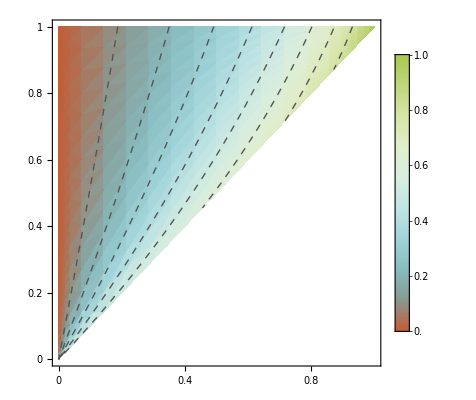

```mathematica
Show[DensityPlot[(s1-(-1+s1) Log[1-s1])/(s1 s2),{s1,0,1},{s2,s1,1}, PlotLegends->Automatic, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(s1-(-1+s1) Log[1-s1])/(s1 s2),{s1,0,1},{s2,s1,1}, ContourShading->None,Contours->8,ContourStyle->Directive[Dashed, Lighter[Black]]]]
```

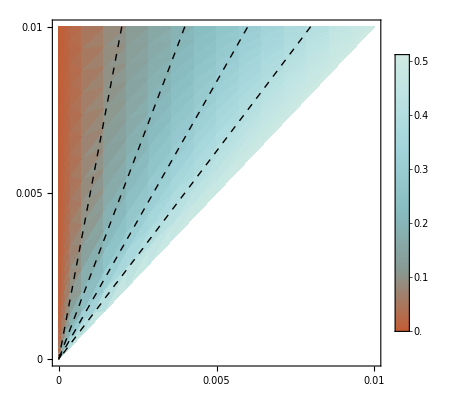

```mathematica
Show[DensityPlot[(s1-(-1+s1) Log[1-s1])/(s1 s2),{s1,0,0.01},{s2,s1,0.01}, PlotLegends->Automatic, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01, 0.015},None},{{0,0.005,0.01, 0.015},None}}, FrameTicksStyle->20], ContourPlot[(s1-(-1+s1) Log[1-s1])/(s1 s2),{s1,0,0.01},{s2,s1,0.01}, ContourShading->None,Contours->4,ContourStyle->Dashed]]
```

```mathematica
dom[s1_,s2_]:=
Piecewise[{{relC1Adom+relC1adom, 0<s2<=1&&0<s1<=s2/2},{relC2Adom+relC2adom, 0<s2<=1&&s2/2<s1<=(2s2)/(2+s2)},{relC3Adom+relC3adom,0<s2<=1&& (2s2)/(2+s2)<s1<=s2}}]
```

```mathematica
domList1=Table[dom[s1,s2],{s2,1/100000,1,0.003},{s1,1/100000,1,0.003}]
```

```mathematica
domList2=Table[dom[s1,s2],{s2,1/100000,0.01,0.00003},{s1,1/100000,0.01,0.00003}]
```

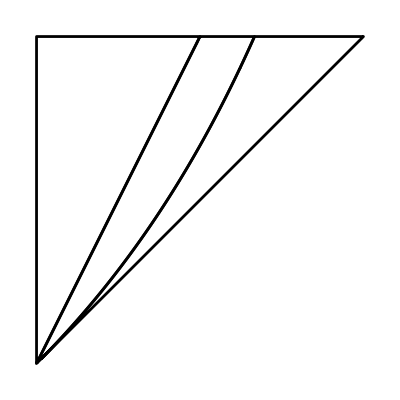
-Graphics--Graphics-

```mathematica
Overlay[{Show[{ListDensityPlot[domList1, ColorFunction->"IslandColors",ColorFunctionScaling->False, Frame->False, PlotRange->{0.25,0.6}, PlotLegends->Automatic],ListContourPlot[domList1, Contours->{0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6}, ContourStyle->Dashed, Frame->False, ContourShading->None, PlotRange->{0.25,0.6}]}],RegionPlot[{0<s1<=s2/2,s2/2<s1<=(2s2)/(2+s2),(2s2)/(2+s2)<s1<=s2}, {s1,0,1}, {s2,s1,1}, MaxRecursion->8,BoundaryStyle->Directive[Thickness[0.005], Black], PlotStyle->None, Frame->False]}, Alignment->{Left, Bottom}]
```

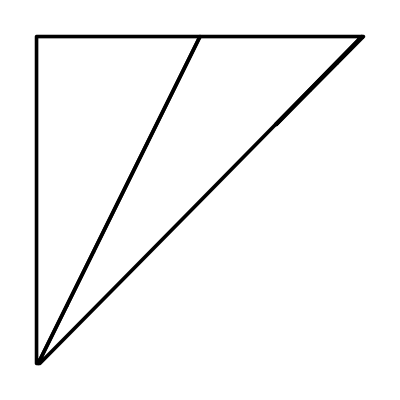
-Graphics--Graphics-

```mathematica
Overlay[{Show[{ListDensityPlot[domList2, ColorFunction->"IslandColors",ColorFunctionScaling->False, Frame->False, PlotRange->{0.25,0.6}],ListContourPlot[domList2, Contours->{0.25,0.3,0.35,0.4, 0.45, 0.5}, ContourStyle->Dashed, Frame->False, ContourShading->None, PlotRange->{0.25,0.6}]}],RegionPlot[{0<s1<=s2/2,s2/2<s1<=(2s2)/(2+s2),(2s2)/(2+s2)<s1<=s2}, {s1,0,0.01}, {s2,s1,0.01}, MaxRecursion->8,BoundaryStyle->Directive[Thickness[0.0065], Black], PlotStyle->None, Frame->False]}, Alignment->{Left, Bottom}]
```

```mathematica
domC[s1_,s2_]:=
Piecewise[{{1.0, 0<s2<=1&&0<s1<=s2/2},{relC2adom/(relC2Adom+relC2adom), 0<s2<=1&&s2/2<s1<=(2s2)/(2+s2)},{relC3adom/(relC3Adom+relC3adom),0<s2<=1&& (2s2)/(2+s2)<s1<=s2}}]
```

```mathematica
domCList1=Table[domC[s1,s2],{s2,1/100000,1,0.003},{s1,1/100000,1,0.003}]
```

```mathematica
domCList2=Table[domC[s1,s2],{s2,1/100000,0.01,0.00003},{s1,1/100000,0.01,0.00003}]
```

```mathematica
Overlay[{Show[{ListDensityPlot[domCList1, ColorFunction->"IslandColors",ColorFunctionScaling->False, Frame->False, PlotRange->{0.4,1.1}, PlotLegends->None],ListContourPlot[domCList1, Contours->{0.4,0.5,0.6, 0.7, 0.8, 0.9,1.0}, ContourStyle->Dashed, Frame->False, ContourShading->None, PlotRange->{0.4,1.1}]}],RegionPlot[{0<s1<=s2/2,s2/2<s1<=(2s2)/(2+s2),(2s2)/(2+s2)<s1<=s2}, {s1,0,1}, {s2,s1,1}, MaxRecursion->8,BoundaryStyle->Directive[Thickness[0.005], Black], PlotStyle->None, Frame->False]}, Alignment->{Left, Bottom}]
```

-Graphics--Graphics-

```mathematica
Overlay[{Show[{ListDensityPlot[domCList2, ColorFunction->"IslandColors",ColorFunctionScaling->False, Frame->False, PlotRange->{0.4,1.1}],ListContourPlot[domCList2, Contours->{0.6, 0.7, 0.8, 0.9}, ContourStyle->Dashed, Frame->False, ContourShading->None, PlotRange->{0.4,1.1}]}],RegionPlot[{0<s1<=s2/2,s2/2<s1<=(2s2)/(2+s2),(2s2)/(2+s2)<s1<=s2}, {s1,0,0.01}, {s2,s1,0.01}, MaxRecursion->8,BoundaryStyle->Directive[Thickness[0.0065], Black], PlotStyle->None, Frame->False]}, Alignment->{Left, Bottom}]
```

-Graphics--Graphics-

```mathematica
domD[s1_,s2_]:=
Piecewise[{{1.0, 0<s2<=1&&0<s1<=s2/2},{1.0, 0<s2<=1&&s2/2<s1<=(2s2)/(2+s2)},{relC3ben/(relC3ben+relC3del),0<s2<=1&& (2s2)/(2+s2)<s1<=s2}}]
```

```mathematica
domDList1=Table[domD[s1,s2],{s2,1/100000,1,0.003},{s1,1/100000,1,0.003}]
```

```mathematica
domDList2=Table[domD[s1,s2],{s2,1/100000,0.01,0.00003},{s1,1/100000,0.01,0.00003}]
```

```mathematica
Overlay[{Show[{ListDensityPlot[domDList1, ColorFunction->"IslandColors",ColorFunctionScaling->False, Frame->False, PlotRange->{0.4,1.1}, PlotLegends->None],ListContourPlot[domDList1, Contours->{0.6,0.7,0.8,0.9}, ContourStyle->Dashed, Frame->False, ContourShading->None, PlotRange->{0.4,1.1}]}],RegionPlot[{0<s1<=s2/2,s2/2<s1<=(2s2)/(2+s2),(2s2)/(2+s2)<s1<=s2}, {s1,0,1}, {s2,s1,1}, MaxRecursion->8,BoundaryStyle->Directive[Thickness[0.005], Black], PlotStyle->None, Frame->False]}, Alignment->{Left, Bottom}]
```

-Graphics--Graphics-

```mathematica
Overlay[{Show[{ListDensityPlot[domDList2, ColorFunction->"IslandColors",ColorFunctionScaling->False, Frame->False, PlotRange->{0.4,1.1}, PlotLegends->None],ListContourPlot[domDList2, Contours->{1.1}, ContourStyle->Dashed, Frame->False, ContourShading->None, PlotRange->{0.4,1.1}]}],RegionPlot[{0<s1<=s2/2,s2/2<s1<=(2s2)/(2+s2),(2s2)/(2+s2)<s1<=s2}, {s1,0,.01}, {s2,s1,.01}, MaxRecursion->8,BoundaryStyle->Directive[Thickness[0.005], Black], PlotStyle->None, Frame->False]}, Alignment->{Left, Bottom}]
```

-Graphics--Graphics-

### Conditions for protected polymorphism (m : 1 generation ratio), incl. Figure 3

#### Q_m region

The region of parameters consistent with overdominance in geometric mean fitness is given below, which assumes an asymmetric distribution of generations per season, where the ratio of season 1 to season 2 is m : 1, and condition 7a in the article:

```mathematica
QmCases=Table[Reduce[(1-h1 s1)^m(1-h2 s2)^1>(1-s1)^m>(1-s2)^1&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1/.{m->i},{s1,s2,h1,h2}], {i,2,6}];
```

```mathematica
QmCases//TableForm
```

0<s1<1&&2 s1-s1^2<s2≤1&&0≤h1<1&&0≤h2<(2 s1-2 h1 s1-s1^2+h1^2 s1^2)/(s2-2 h1 s1 s2+h1^2 s1^2 s2)
0<s1<1&&3 s1-3 s1^2+s1^3<s2≤1&&0≤h1<1&&0≤h2<(-3 s1+3 h1 s1+3 s1^2-3 h1^2 s1^2-s1^3+h1^3 s1^3)/(-s2+3 h1 s1 s2-3 h1^2 s1^2 s2+h1^3 s1^3 s2)
0<s1<1&&4 s1-6 s1^2+4 s1^3-s1^4<s2≤1&&0≤h1<1&&0≤h2<(4 s1-4 h1 s1-6 s1^2+6 h1^2 s1^2+4 s1^3-4 h1^3 s1^3-s1^4+h1^4 s1^4)/(s2-4 h1 s1 s2+6 h1^2 s1^2 s2-4 h1^3 s1^3 s2+h1^4 s1^4 s2)
0<s1<1&&5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5<s2≤1&&0≤h1<1&&0≤h2<(-5 s1+5 h1 s1+10 s1^2-10 h1^2 s1^2-10 s1^3+10 h1^3 s1^3+5 s1^4-5 h1^4 s1^4-s1^5+h1^5 s1^5)/(-s2+5 h1 s1 s2-10 h1^2 s1^2 s2+10 h1^3 s1^3 s2-5 h1^4 s1^4 s2+h1^5 s1^5 s2)
0<s1<1&&6 s1-15 s1^2+20 s1^3-15 s1^4+6 s1^5-s1^6<s2≤1&&0≤h1<1&&0≤h2<(6 s1-6 h1 s1-15 s1^2+15 h1^2 s1^2+20 s1^3-20 h1^3 s1^3-15 s1^4+15 h1^4 s1^4+6 s1^5-6 h1^5 s1^5-s1^6+h1^6 s1^6)/(s2-6 h1 s1 s2+15 h1^2 s1^2 s2-20 h1^3 s1^3 s2+15 h1^4 s1^4 s2-6 h1^5 s1^5 s2+h1^6 s1^6 s2)

The lower bound on the season 2 selection coefficient is equal to 1-(1-s_1)^m, which may be interpreted as the “seasonally-cumulative” selection coefficient associated with the overall season 1 fitness (as opposed to the single-generation season 1 fitness). This expression was derived by noticing that the s_2 minimal bounds (output above) depends on summing the binomial coefficients from 1 to the total number of season 1 generations,  multiplying each binomial coefficient by the corresponding power of s_1 and alternating signs between successive terms in the manner made explicit below:

```mathematica
∑_(k=1)^m ((-1)^(k-1)Binomial[m,k] s1^k)
```

1-(1-s1)^m

Confirmation:

```mathematica
Table[1-(1-s1)^m/.m->i//Expand, {i,2,6}]
```

{2 s1-s1^2,3 s1-3 s1^2+s1^3,4 s1-6 s1^2+4 s1^3-s1^4,5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5,6 s1-15 s1^2+20 s1^3-15 s1^4+6 s1^5-s1^6}

```mathematica
QmCases[[All,2]][[All,1]]
```

{2 s1-s1^2,3 s1-3 s1^2+s1^3,4 s1-6 s1^2+4 s1^3-s1^4,5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5,6 s1-15 s1^2+20 s1^3-15 s1^4+6 s1^5-s1^6}

The upper bound on the season 2 dominance coefficient (h_(2,max)^(m)) is equal to  ((-1)^m((1-h_1 s_1)^m-(1-s_1)^m))/(s_2(h_1 s_1-1))^m. This expression was derived by discerning that the following equation (input below) reproduces the dominance bound for any m. After entering the equation, it is seen to simplify (note the elimination of the binomial coefficient function and summation symbol from the output expression):

```mathematica
((-1)^m∑_(k=1)^m ((-1)^k Binomial[m,k](h1^k-1)s1^k))/(s2 (h1 s1 -1)^m)//FullSimplify
```

((-1)^m (-1+h1 s1)^-m (-(1-s1)^m+(1-h1 s1)^m))/s2

Confirmation:

```mathematica
Reduce[QmCases[[All,4]][[All,5]]==Table[Expand[Numerator[((-1)^m((1-h1 s1)^m-(1-s1)^m))/(s2(-1+h1 s1)^m)/.m->i]]/Expand[Denominator[((-1)^m((1-h1 s1)^m-(1-s1)^m))/(s2(-1+h1 s1)^m)/.m->i]],{i, 2, 6}]]
```

True

The h_(2,max)^(m) function is integrated from 0 to 1 to derive the area formula for the Q_m region for cases of m = 2 through m = 6:

```mathematica
areasQm =Table[Assuming[0<s1<=1&&0<s2<1-(1-s1)^m/.m->i,Integrate[((-1)^m((1-h1 s1)^m-(1-s1)^m))/(s2(-1+h1 s1)^m)/.m->i,{h1,0,1}]],{i, 2, 6}]
```

{s1/s2,-((-3+s1) s1)/(2 s2),(s1 (6-4 s1+s1^2))/(3 s2),-(s1 (-10+s1 (10+(-5+s1) s1)))/(4 s2),(s1 (15+s1 (-20+s1 (15+(-6+s1) s1))))/(5 s2)}

```mathematica
Table[Expand[Numerator[areas[[i]]]]/Expand[Denominator[areas[[i]]]],{i,1,5}]
```

{s1/s2,(3 s1-s1^2)/(2 s2),(6 s1-4 s1^2+s1^3)/(3 s2),(10 s1-10 s1^2+5 s1^3-s1^4)/(4 s2),(15 s1-20 s1^2+15 s1^3-6 s1^4+s1^5)/(5 s2)}

Clearly the denominators for these special cases follow the general pattern (m-1)s_2. [The first element above is for the case m = 2]. I discerned the numerators to follow the general pattern:

```mathematica
∑_(k=2)^m ((-1)^k Binomial[m,k] s1^(k-1))
```

(-1+(1-s1)^m+m s1)/s1

And so the general formula for the Area(Q_m):

```mathematica
(-1+(1-s1)^m+m s1)/((m-1)s1 s2);
```

Confirmation:

```mathematica
Reduce[Table[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->i, {i, 2, 6}]==areasQm]
```

True

#### R_m region

The region of parameters consistent with overdominance in geometric mean fitness is given below, which assumes an asymmetric distribution of generations per season, where the ratio of m : n is m : 1, and condition 7b in the article:

```mathematica
RmCases=Table[Reduce[(1-h1 s1)^m(1-h2 s2)^1>(1-s2)^1>(1-s1)^m&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1/.{m->i},{s1,s2,h2,h1}], {i,{2,3,4,5,10}}];
```

```mathematica
RmCases//TableForm
```

0<s1≤1&&0<s2<2 s1-s1^2&&0≤h2<1&&0≤h1<1/s1-√((-1+s2)/(s1^2 (-1+h2 s2)))
0<s1≤1&&0<s2<3 s1-3 s1^2+s1^3&&0≤h2<1&&0≤h1<Root[s2-h2 s2+(-3 s1+3 h2 s1 s2) #1+(3 s1^2-3 h2 s1^2 s2) #1^2+(-s1^3+h2 s1^3 s2) #1^3&,1]
0<s1≤1&&0<s2<4 s1-6 s1^2+4 s1^3-s1^4&&0≤h2<1&&0≤h1<Root[-s2+h2 s2+(4 s1-4 h2 s1 s2) #1+(-6 s1^2+6 h2 s1^2 s2) #1^2+(4 s1^3-4 h2 s1^3 s2) #1^3+(-s1^4+h2 s1^4 s2) #1^4&,1]
0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5&&0≤h2<1&&0≤h1<Root[s2-h2 s2+(-5 s1+5 h2 s1 s2) #1+(10 s1^2-10 h2 s1^2 s2) #1^2+(-10 s1^3+10 h2 s1^3 s2) #1^3+(5 s1^4-5 h2 s1^4 s2) #1^4+(-s1^5+h2 s1^5 s2) #1^5&,1]
0<s1≤1&&0<s2<10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10&&0≤h2<1&&0≤h1<Root[-s2+h2 s2+(10 s1-10 h2 s1 s2) #1+(-45 s1^2+45 h2 s1^2 s2) #1^2+(120 s1^3-120 h2 s1^3 s2) #1^3+(-210 s1^4+210 h2 s1^4 s2) #1^4+(252 s1^5-252 h2 s1^5 s2) #1^5+(-210 s1^6+210 h2 s1^6 s2) #1^6+(120 s1^7-120 h2 s1^7 s2) #1^7+(-45 s1^8+45 h2 s1^8 s2) #1^8+(10 s1^9-10 h2 s1^9 s2) #1^9+(-s1^10+h2 s1^10 s2) #1^10&,1]

An alternative representation of region R_m (re-arranging the order of dominance coefficients in the outputs):

```mathematica
RmCases2=Table[Reduce[(1-h1 s1)^m(1-h2 s2)^1>(1-s2)^1>(1-s1)^m&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1/.{m->i},{s1,s2,h1,h2}], {i,{2,3,4,5,10}}];
```

```mathematica
RmCases2//TableForm
```

0<s1≤1&&0<s2<2 s1-s1^2&&0≤h1<1/s1-√((1-s2)/s1^2)&&0≤h2<(-2 h1 s1+h1^2 s1^2+s2)/(s2-2 h1 s1 s2+h1^2 s1^2 s2)
0<s1≤1&&0<s2<3 s1-3 s1^2+s1^3&&0≤h1<Root[-s2+3 s1 #1-3 s1^2 #1^2+s1^3 #1^3&,1]&&0≤h2<(3 h1 s1-3 h1^2 s1^2+h1^3 s1^3-s2)/(-s2+3 h1 s1 s2-3 h1^2 s1^2 s2+h1^3 s1^3 s2)
0<s1≤1&&0<s2<4 s1-6 s1^2+4 s1^3-s1^4&&0≤h1<Root[s2-4 s1 #1+6 s1^2 #1^2-4 s1^3 #1^3+s1^4 #1^4&,1]&&0≤h2<(-4 h1 s1+6 h1^2 s1^2-4 h1^3 s1^3+h1^4 s1^4+s2)/(s2-4 h1 s1 s2+6 h1^2 s1^2 s2-4 h1^3 s1^3 s2+h1^4 s1^4 s2)
0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5&&0≤h1<Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]&&0≤h2<(5 h1 s1-10 h1^2 s1^2+10 h1^3 s1^3-5 h1^4 s1^4+h1^5 s1^5-s2)/(-s2+5 h1 s1 s2-10 h1^2 s1^2 s2+10 h1^3 s1^3 s2-5 h1^4 s1^4 s2+h1^5 s1^5 s2)
0<s1≤1&&0<s2<10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10&&0≤h1<Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]&&0≤h2<(-10 h1 s1+45 h1^2 s1^2-120 h1^3 s1^3+210 h1^4 s1^4-252 h1^5 s1^5+210 h1^6 s1^6-120 h1^7 s1^7+45 h1^8 s1^8-10 h1^9 s1^9+h1^10 s1^10+s2)/(s2-10 h1 s1 s2+45 h1^2 s1^2 s2-120 h1^3 s1^3 s2+210 h1^4 s1^4 s2-252 h1^5 s1^5 s2+210 h1^6 s1^6 s2-120 h1^7 s1^7 s2+45 h1^8 s1^8 s2-10 h1^9 s1^9 s2+h1^10 s1^10 s2)

The upper bound on the season 2 selection coefficient is equal to 1-(1-s_1)^m. [This was the lower bound in the Q_m region]

```mathematica
∑_(k=1)^m ((-1)^(k-1)Binomial[m,k] s1^k)
```

1-(1-s1)^m

The upper bound on the season 1 dominance coefficient (η_(1,max)^(m)) is the smallest real root of the polynomial: (1-h_2 s_2)(1-η_(1,max)^(m)s_1 )^m+ s_2-1 . This expression was derived by discerning that the following equation (input below, note both m replacements) reproduces the dominance bound for any m.

```mathematica
Root[Total[Table[(-1)^(k)Binomial[m,k]( s1^k- h2 s1^k s2)#1^k,{k,1,m/.m->3}]]+s2-h2 s2&,1]/.m->3
```

Root[s2-h2 s2+(-3 s1+3 h2 s1 s2) #1+(3 s1^2-3 h2 s1^2 s2) #1^2+(-s1^3+h2 s1^3 s2) #1^3&,1]

After entering the general form of the equation, it is seen to simplify (note the elimination of the binomial coefficient function and summation symbol from the output expression):

```mathematica
s2-h2 s2+∑_(k=1)^m (-1)^k Binomial[m,k]( s1^k- h2 s1^k s2)#1^k
```

s2-h2 s2-(-1+h2 s2) (-1+(1-s1 #1)^m)

```mathematica
eta1max=s2-h2 s2-(-1+h2 s2) (-1+(1-s1 #1)^m)&//FullSimplify
```

s2-h2 s2-(-1+h2 s2) (-1+(1-s1 #1)^m)&

The η_(1,max)^(m) function is integrated from 0 to 1 to derive the area formula for the R_m region for cases of m = 2 through m = 5:

```mathematica
areasRm=Table[Assuming[0<s1≤1&&0<s2<1-(1-s1)^m/.m->i,Integrate[Root[eta1max/.m->i,1],{h2,0,1}]],{i,{2,3,4,5}}]
```

{-(-2+2 √(1-s2)+s2)/(s1 s2),-(-3+3 (1-s2)^(1/3)+s2)/(2 s1 s2),-(-4+4 (1-s2)^(1/4)+s2)/(3 s1 s2),∫_0^1 Root[s2-h2 s2+(-5 s1+5 h2 s1 s2) #1+(10 s1^2-10 h2 s1^2 s2) #1^2+(-10 s1^3+10 h2 s1^3 s2) #1^3+(5 s1^4-5 h2 s1^4 s2) #1^4+(-s1^5+h2 s1^5 s2) #1^5&,1]ⅆh2}

The case for m = 5 did not evaluate, but the first three terms suggest the general equation Area(R_m) = (m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)

```mathematica
(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2);
```

A derivation of Area(R_5) is possible by using the “alternative” representation of R_m derived several lines above:

```mathematica
Table[Assuming[0<s1≤1&&0<s2<1-(1-s1)^m/.m->i,Integrate[(5 h1 s1-10 h1^2 s1^2+10 h1^3 s1^3-5 h1^4 s1^4+h1^5 s1^5-s2)/(-s2+5 h1 s1 s2-10 h1^2 s1^2 s2+10 h1^3 s1^3 s2-5 h1^4 s1^4 s2+h1^5 s1^5 s2),{h1,0,Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]}]],{i,{5}}]
```

{(Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]+((-1+s2) (-1+1/((-1+s1 Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1])^4)))/(4 s1))/s2}

This is a complicated expression, and not obviously equal to Area(R_m) = (m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2) for m = 5. But numerical evaluation demonstrates that the general formula gives the correct answer:

```mathematica
{(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2),(Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]+((-1+s2) (-1+1/((-1+s1 Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1])^4)))/(4 s1))/s2}/.{s1->0.03, s2->0.005,m->5}
```

{0.0167168,0.0167168}

Area(R_m) = (m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2) is concluded to be the correct formula when W(AA) > W(aa).

#### Figure 3

```mathematica
GraphicsGrid[{{Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->2,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->2, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->2,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->2, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]],DensityPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->2,{s1,0,1},{s2,0,1-(1-s1)^m}/.m->2, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->2,{s1,0,1},{s2,0,1-(1-s1)^m}/.m->2, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->5,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->5, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->5,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->5, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]],DensityPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->5,{s1,0,1},{s2,0,1-(1-s1)^m}/.m->5, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->5,{s1,0,1},{s2,0,1-(1-s1)^m}/.m->5, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->2,{s1,0,0.005},{s2,1-(1-s1)^m,0.01}/.m->2, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.0025, 0.005},None}}, FrameTicksStyle->20], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->2,{s1,0,0.005},{s2,1-(1-s1)^m,0.01}/.m->2, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]],DensityPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->2,{s1,0,0.005},{s2,0,1-(1-s1)^m}/.m->2, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.0025, 0.005},None}}, FrameTicksStyle->20], ContourPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->2,{s1,0,0.005},{s2,0,1-(1-s1)^m}/.m->2, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->5,{s1,0,0.002},{s2,1-(1-s1)^m,0.01}/.m->5, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.001, 0.002},None}}, FrameTicksStyle->20], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->5,{s1,0,0.002},{s2,1-(1-s1)^m,0.01}/.m->5, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]],DensityPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->5,{s1,0,0.002},{s2,0,1-(1-s1)^m}/.m->5, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.001, 0.002},None}}, FrameTicksStyle->20], ContourPlot[(m-m(1-s2)^(1/m)-s2)/((m-1)s1 s2)/.m->5,{s1,0,0.002},{s2,0,1-(1-s1)^m}/.m->5, ContourShading->None,Contours->{0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]]}}]
```

-Graphics-

```mathematica
QmCases2=Table[Reduce[(1-h1 s1)^m(1-h2 s2)^1>(1-s2)^1>(1-s1)^m&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1/.{m->i},{s1,s2,h2,h1}], {i,{2,3,4,5,10}}];
```

```mathematica
QmCases2
```

{0<s1≤1&&0<s2<2 s1-s1^2&&0≤h2<1&&0≤h1<1/s1-√((-1+s2)/(s1^2 (-1+h2 s2))),0<s1≤1&&0<s2<3 s1-3 s1^2+s1^3&&0≤h2<1&&0≤h1<Root[s2-h2 s2+(-3 s1+3 h2 s1 s2) #1+(3 s1^2-3 h2 s1^2 s2) #1^2+(-s1^3+h2 s1^3 s2) #1^3&,1],0<s1≤1&&0<s2<4 s1-6 s1^2+4 s1^3-s1^4&&0≤h2<1&&0≤h1<Root[-s2+h2 s2+(4 s1-4 h2 s1 s2) #1+(-6 s1^2+6 h2 s1^2 s2) #1^2+(4 s1^3-4 h2 s1^3 s2) #1^3+(-s1^4+h2 s1^4 s2) #1^4&,1],0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5&&0≤h2<1&&0≤h1<Root[s2-h2 s2+(-5 s1+5 h2 s1 s2) #1+(10 s1^2-10 h2 s1^2 s2) #1^2+(-10 s1^3+10 h2 s1^3 s2) #1^3+(5 s1^4-5 h2 s1^4 s2) #1^4+(-s1^5+h2 s1^5 s2) #1^5&,1],0<s1≤1&&0<s2<10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10&&0≤h2<1&&0≤h1<Root[-s2+h2 s2+(10 s1-10 h2 s1 s2) #1+(-45 s1^2+45 h2 s1^2 s2) #1^2+(120 s1^3-120 h2 s1^3 s2) #1^3+(-210 s1^4+210 h2 s1^4 s2) #1^4+(252 s1^5-252 h2 s1^5 s2) #1^5+(-210 s1^6+210 h2 s1^6 s2) #1^6+(120 s1^7-120 h2 s1^7 s2) #1^7+(-45 s1^8+45 h2 s1^8 s2) #1^8+(10 s1^9-10 h2 s1^9 s2) #1^9+(-s1^10+h2 s1^10 s2) #1^10&,1]}

```mathematica
out2b=Assuming[0<s1≤1&&0<s2<2 s1-s1^2,Integrate[1/s1-√((-1+s2)/(s1^2 (-1+h2 s2))),{h2,0,1}]]//FullSimplify;
```

```mathematica
-(-2+2 √(1-s2)+s2)/(s1 s2)
```

-(-2+2 √(1-s2)+s2)/(s1 s2)

```mathematica
out3b=Assuming[0<s1≤1&&0<s2<3 s1-3 s1^2+s1^3,Integrate[Root[s2-h2 s2+(-3 s1+3 h2 s1 s2) #1+(3 s1^2-3 h2 s1^2 s2) #1^2+(-s1^3+h2 s1^3 s2) #1^3&,1],{h2,0,1}]]//FullSimplify;
```

```mathematica
-(-3+3 (1-s2)^(1/3)+s2)/(2 s1 s2)
```

-(-3+3 (1-s2)^(1/3)+s2)/(2 s1 s2)

```mathematica
out4b=Assuming[0<s1≤1&&0<s2<4 s1-6 s1^2+4 s1^3-s1^4,Integrate[Root[-s2+h2 s2+(4 s1-4 h2 s1 s2) #1+(-6 s1^2+6 h2 s1^2 s2) #1^2+(4 s1^3-4 h2 s1^3 s2) #1^3+(-s1^4+h2 s1^4 s2) #1^4&,1],{h2,0,1}]]//FullSimplify;
```

```mathematica
-(-4+4 (1-s2)^(1/4)+s2)/(3 s1 s2)
```

-(-4+4 (1-s2)^(1/4)+s2)/(3 s1 s2)

```mathematica
out5b=Assuming[0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5,Integrate[(-10 h1 s1+45 h1^2 s1^2-120 h1^3 s1^3+210 h1^4 s1^4-252 h1^5 s1^5+210 h1^6 s1^6-120 h1^7 s1^7+45 h1^8 s1^8-10 h1^9 s1^9+h1^10 s1^10+s2)/(s2-10 h1 s1 s2+45 h1^2 s1^2 s2-120 h1^3 s1^3 s2+210 h1^4 s1^4 s2-252 h1^5 s1^5 s2+210 h1^6 s1^6 s2-120 h1^7 s1^7 s2+45 h1^8 s1^8 s2-10 h1^9 s1^9 s2+h1^10 s1^10 s2),{h2,0,1}]]//FullSimplify;
```

```mathematica
{out2,out3,out4,out5}//TableForm
```

```mathematica
QmCases=Table[Reduce[(1-h1 s1)^m(1-h2 s2)^1>(1-s2)^1>(1-s1)^m&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1/.{m->i},{s1,s2,h1,h2}], {i,{2,3,4,5,10}}];
```

```mathematica
QmCases//TableForm
```

0<s1≤1&&0<s2<2 s1-s1^2&&0≤h1<1/s1-√((1-s2)/s1^2)&&0≤h2<(-2 h1 s1+h1^2 s1^2+s2)/(s2-2 h1 s1 s2+h1^2 s1^2 s2)
0<s1≤1&&0<s2<3 s1-3 s1^2+s1^3&&0≤h1<Root[-s2+3 s1 #1-3 s1^2 #1^2+s1^3 #1^3&,1]&&0≤h2<(3 h1 s1-3 h1^2 s1^2+h1^3 s1^3-s2)/(-s2+3 h1 s1 s2-3 h1^2 s1^2 s2+h1^3 s1^3 s2)
0<s1≤1&&0<s2<4 s1-6 s1^2+4 s1^3-s1^4&&0≤h1<Root[s2-4 s1 #1+6 s1^2 #1^2-4 s1^3 #1^3+s1^4 #1^4&,1]&&0≤h2<(-4 h1 s1+6 h1^2 s1^2-4 h1^3 s1^3+h1^4 s1^4+s2)/(s2-4 h1 s1 s2+6 h1^2 s1^2 s2-4 h1^3 s1^3 s2+h1^4 s1^4 s2)
0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5&&0≤h1<Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]&&0≤h2<(5 h1 s1-10 h1^2 s1^2+10 h1^3 s1^3-5 h1^4 s1^4+h1^5 s1^5-s2)/(-s2+5 h1 s1 s2-10 h1^2 s1^2 s2+10 h1^3 s1^3 s2-5 h1^4 s1^4 s2+h1^5 s1^5 s2)
0<s1≤1&&0<s2<10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10&&0≤h1<Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]&&0≤h2<(-10 h1 s1+45 h1^2 s1^2-120 h1^3 s1^3+210 h1^4 s1^4-252 h1^5 s1^5+210 h1^6 s1^6-120 h1^7 s1^7+45 h1^8 s1^8-10 h1^9 s1^9+h1^10 s1^10+s2)/(s2-10 h1 s1 s2+45 h1^2 s1^2 s2-120 h1^3 s1^3 s2+210 h1^4 s1^4 s2-252 h1^5 s1^5 s2+210 h1^6 s1^6 s2-120 h1^7 s1^7 s2+45 h1^8 s1^8 s2-10 h1^9 s1^9 s2+h1^10 s1^10 s2)

```mathematica
Total[Table[(-1)^(k-1) Binomial[3,k] s1^k#1^k,{k,1,3}]]-s2
```

-s2+3 s1 #1-3 s1^2 #1^2+s1^3 #1^3

```mathematica
-s2+∑_(k=1)^m (-1)^(k-1)Binomial[m,k] s1^k#1^k
```

1-s2-(1-s1 #1)^m

```mathematica
out2=Assuming[0<s1≤1&&0<s2<2 s1-s1^2,Integrate[(-2 h1 s1+h1^2 s1^2+s2)/(s2-2 h1 s1 s2+h1^2 s1^2 s2),{h1,0,1/s1-√((1-s2)/s1^2)}]]//FullSimplify;
```

```mathematica
out3=Assuming[0<s1≤1&&0<s2<3 s1-3 s1^2+s1^3,Integrate[(3 h1 s1-3 h1^2 s1^2+h1^3 s1^3-s2)/(-s2+3 h1 s1 s2-3 h1^2 s1^2 s2+h1^3 s1^3 s2),{h1,0,Root[-s2+3 s1 #1-3 s1^2 #1^2+s1^3 #1^3&,1]}]]//FullSimplify;
```

```mathematica
out4=Assuming[0<s1≤1&&0<s2<4 s1-6 s1^2+4 s1^3-s1^4,Integrate[(-4 h1 s1+6 h1^2 s1^2-4 h1^3 s1^3+h1^4 s1^4+s2)/(s2-4 h1 s1 s2+6 h1^2 s1^2 s2-4 h1^3 s1^3 s2+h1^4 s1^4 s2),{h1,0,Root[s2-4 s1 #1+6 s1^2 #1^2-4 s1^3 #1^3+s1^4 #1^4&,1]}]]//FullSimplify;
```

```mathematica
out5=Assuming[0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5,Integrate[(-10 h1 s1+45 h1^2 s1^2-120 h1^3 s1^3+210 h1^4 s1^4-252 h1^5 s1^5+210 h1^6 s1^6-120 h1^7 s1^7+45 h1^8 s1^8-10 h1^9 s1^9+h1^10 s1^10+s2)/(s2-10 h1 s1 s2+45 h1^2 s1^2 s2-120 h1^3 s1^3 s2+210 h1^4 s1^4 s2-252 h1^5 s1^5 s2+210 h1^6 s1^6 s2-120 h1^7 s1^7 s2+45 h1^8 s1^8 s2-10 h1^9 s1^9 s2+h1^10 s1^10 s2),{h1,0,Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]}]]//FullSimplify;
```

```mathematica
{out2,out3,out4,out5}//TableForm
```

-(-2+2 √(1-s2)+s2)/(s1 s2)
(Root[-s2+3 s1 #1-3 s1^2 #1^2+s1^3 #1^3&,1]+((-1+s2) (-1+1/((-1+s1 Root[-s2+3 s1 #1-3 s1^2 #1^2+s1^3 #1^3&,1])^2)))/(2 s1))/s2
-(-4+4 (1-s2)^(1/4)+s2)/(3 s1 s2)
ConditionalExpression[1/(9 s2)(9 Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]+(1-s2+(1-s2)/((-1+s1 Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1])^9))/s1), ]

```mathematica
out7b1=Assuming[0<s1≤1&&0<s2<2 s1-s1^2,Integrate[(-2 h1 s1+h1^2 s1^2+s2)/(s2-2 h1 s1 s2+h1^2 s1^2 s2),{h1,0,1/s1-√((1-s2)/s1^2)}]]//FullSimplify;
```

```mathematica
out7b2=Assuming[0<s1≤1&&0<s2<5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5,Integrate[(5 h1 s1-10 h1^2 s1^2+10 h1^3 s1^3-5 h1^4 s1^4+h1^5 s1^5-s2)/(-s2+5 h1 s1 s2-10 h1^2 s1^2 s2+10 h1^3 s1^3 s2-5 h1^4 s1^4 s2+h1^5 s1^5 s2),{h1,0,Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]}]];
```

```mathematica
out7b3=Assuming[0<s1≤1&&0<s2<10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10,Integrate[(-10 h1 s1+45 h1^2 s1^2-120 h1^3 s1^3+210 h1^4 s1^4-252 h1^5 s1^5+210 h1^6 s1^6-120 h1^7 s1^7+45 h1^8 s1^8-10 h1^9 s1^9+h1^10 s1^10+s2)/(s2-10 h1 s1 s2+45 h1^2 s1^2 s2-120 h1^3 s1^3 s2+210 h1^4 s1^4 s2-252 h1^5 s1^5 s2+210 h1^6 s1^6 s2-120 h1^7 s1^7 s2+45 h1^8 s1^8 s2-10 h1^9 s1^9 s2+h1^10 s1^10 s2),{h1,0,Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]}]][[1]];
```

```mathematica
-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5
```

```mathematica
-9 s2+9 s1 (5+4 s2)//Expand
```

45 s1-9 s2+36 s1 s2

```mathematica
{out7b1,out7b2, out7b3}
```

{-(-2+2 √(1-s2)+s2)/(s1 s2),(Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1]+((-1+s2) (-1+1/((-1+s1 Root[-s2+5 s1 #1-10 s1^2 #1^2+10 s1^3 #1^3-5 s1^4 #1^4+s1^5 #1^5&,1])^4)))/(4 s1))/s2,(Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1] (-9 s2+9 s1 (5+4 s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]-12 s1^2 (20+7 s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^2+126 s1^3 (5+s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^3-126 s1^4 (8+s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^4+42 s1^5 (25+2 s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^5-36 s1^6 (20+s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^6+9 s1^7 (35+s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^7-s1^8 (80+s2) Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^8+9 s1^9 Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1]^9))/(9 s2 (-1+s1 Root[s2-10 s1 #1+45 s1^2 #1^2-120 s1^3 #1^3+210 s1^4 #1^4-252 s1^5 #1^5+210 s1^6 #1^6-120 s1^7 #1^7+45 s1^8 #1^8-10 s1^9 #1^9+s1^10 #1^10&,1])^9)}

```mathematica
GraphicsGrid[{{Show[DensityPlot[out7b1,{s1,0,1},{s2,0,2 s1-s1^2}, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[out7b1,{s1,0,1},{s2,0,2 s1-s1^2}, ContourShading->None,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[out7b2,{s1,0,1},{s2,0,5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5}, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[out7b2,{s1,0,1},{s2,0,5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5}, ContourShading->None,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[out7b3,{s1,0,1},{s2,0,10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10}, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[out7b3,{s1,0,1},{s2,0,10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10}, ContourShading->None,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{Show[DensityPlot[out7b1,{s1,0,0.005},{s2,0,2 s1-s1^2}, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.0025, 0.005},None}}, FrameTicksStyle->20], ContourPlot[out7b1,{s1,0,0.005},{s2,0,2 s1-s1^2}, ContourShading->None,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[out7b2,{s1,0,0.002},{s2,0,5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5}, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.001, 0.002},None}}, FrameTicksStyle->20], ContourPlot[out7b2,{s1,0,0.002},{s2,0,5 s1-10 s1^2+10 s1^3-5 s1^4+s1^5}, ContourShading->None,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[out7b3,{s1,0,0.001},{s2,0,10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10}, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.005,0.01},None},{{0,0.0005,0.001},None}}, FrameTicksStyle->20], ContourPlot[out7b3,{s1,0,0.001},{s2,0,10 s1-45 s1^2+120 s1^3-210 s1^4+252 s1^5-210 s1^6+120 s1^7-45 s1^8+10 s1^9-s1^10}, ContourShading->None,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourStyle->Directive[Dashed, Lighter[Black]]]]}}]
```

-Graphics-

```mathematica
-(-3+3 (1-s2)^(1/3)+s2)/(2 s1 s2)
```

```mathematica
-(-m+m (1-s2)^(1/m)+s2)/((-1+m) s1 s2)/.{s1->Subscript[s, 1], s2->Subscript[s, 2]}//TraditionalForm
```

-(m (1-s_2)^(1/m)-m+s_2)/((m-1) s_1 s_2)

```mathematica
{(-1+(1-s1)^m+m s1)/((m-1)s1 s2), (-m+m(1-s2)^(1/m)+s2)/((m-1)s1 s2)}
```

{(-1+(1-s1)^m+m s1)/((-1+m) s1 s2),(-m+m (1-s2)^(1/m)+s2)/((-1+m) s1 s2)}

```mathematica
AreaPm=Piecewise[{{(-1+(1-s1)^m+m s1)/((-1+m) s1 s2), 0<=s1<1&&1-(1-s1)^m<=s2<1},{ (-m+m(1-s2)^(1/m)+s2)/((m-1)s1 s2), 0<=s1<1&&0<=s2<1-(1-s1)^m}}]
```

Piecewise[{{(-1+(1-s1)^m+m s1)/((-1+m) s1 s2), 0≤s1<1&&1-(1-s1)^m≤s2<1}, {(-m+m (1-s2)^(1/m)+s2)/((-1+m) s1 s2), 0≤s1<1&&0≤s2<1-(1-s1)^m}, {0, True}}]

```mathematica
ContourPlot[(m-m (1-s2)^(1/m)-s2)/((-1+m) s1 s2)/.m->2,{s1,0,1},{s2,0,1}/.m->2, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16]
```

-Graphics-

```mathematica
GraphicsGrid[{{Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->2,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->2, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->2,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->2, ContourShading->None,Contours->9,ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->5,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->5, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->5,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->5, ContourShading->None,Contours->9,ContourStyle->Directive[Dashed, Lighter[Black]]]],Show[DensityPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->10,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->10, ColorFunction->"IslandColors", ColorFunctionScaling->False, Frame->True,FrameTicks->{{{0,0.2,0.4, 0.6, 0.8, 1},None},{{0,0.2,0.4, 0.6, 0.8, 1},None}}, FrameTicksStyle->16], ContourPlot[(-1+(1-s1)^m+m s1)/((m-1)s1 s2)/.m->10,{s1,0,1},{s2,1-(1-s1)^m,1}/.m->10, ContourShading->None,Contours->9,ContourStyle->Directive[Dashed, Lighter[Black]]]]}}]
```

### Numerical distribution

```mathematica
smallm1n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->1, n->1},100000];
```

```mathematica
smallm2n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->2, n->1},100000];
```

```mathematica
smallm5n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->5, n->1},100000];
```

```mathematica
smallm10n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->10, n->1},100000];
```

```mathematica
medm1n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->1, n->1},100000];
```

```mathematica
medm2n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->2, n->1},100000];
```

```mathematica
medm5n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->5, n->1},100000];
```

```mathematica
medm10n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->10, n->1},100000];
```

```mathematica
largem1n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->1, n->1},100000];
```

```mathematica
largem2n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->2, n->1},100000];
```

```mathematica
largem5n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->5, n->1},100000];
```

```mathematica
largem10n1a=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s1)^m>=(1-s2)^n)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->10, n->1},100000];
```

```mathematica
smallm1n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->1, n->1},100000];
```

```mathematica
smallm2n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->2, n->1},100000];
```

```mathematica
smallm5n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->5, n->1},100000];
```

```mathematica
smallm10n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1/1000&&0<=s2<=1/1000,{s1,s2,h1,h2}]/.{m->10, n->1},100000];
```

```mathematica
medm1n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->1, n->1},100000];
```

```mathematica
medm2n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->2, n->1},100000];
```

```mathematica
medm5n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->5, n->1},100000];
```

```mathematica
medm10n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&1/1000<=s1<=10/100&&1/1000<=s2<=10/100,{s1,s2,h1,h2}]/.{m->10, n->1},100000];
```

```mathematica
largem1n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->1, n->1},100000];
```

```mathematica
largem2n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->2, n->1},100000];
```

```mathematica
largem5n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->5, n->1},100000];
```

```mathematica
largem10n1b=RandomPoint[ImplicitRegion[((1-h1 s1)^m (1-h2 s2)^n>(1-s2)^n>=(1-s1)^m)&&0<=h1<=1&&0<=h2<=1&&10/100<=s1<=1&&10/100<=s2<=1,{s1,s2,h1,h2}]/.{m->10, n->1},100000];
```

```mathematica
parameterSETS = {smallm1n1a,smallm2n1a,smallm5n1a,smallm10n1a,medm1n1a,medm2n1a,medm5n1a,medm10n1a,largem1n1a,largem2n1a,largem5n1a,largem10n1a,smallm1n1b,smallm2n1b,smallm5n1b,smallm10n1b,medm1n1b,medm2n1b,medm5n1b,medm10n1b,largem1n1b,largem2n1b,largem5n1b,largem10n1b};
```

```mathematica
Save["SSDparametersets.wl", parameterSETS]
```

```mathematica
quadbars[points_]:= {Count[points,{_,_,h1_, h2_}/;h1<0.5&&h2<0.5],Count[points,{_,_,h1_, h2_}/;h1>0.5&&h2<0.5],Count[points,{_,_,h1_, h2_}/;h1<0.5&&h2>0.5],Count[points,{_,_,h1_, h2_}/;h1>0.5&&h2>0.5]}
```

```mathematica
GraphicsGrid[{{BarChart[quadbars/@{smallm1n1a,medm1n1a, largem1n1a}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple} ],BarChart[quadbars/@{smallm2n1a,medm2n1a, largem2n1a}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple}],BarChart[quadbars/@{smallm5n1a,medm5n1a, largem5n1a}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple}],BarChart[quadbars/@{smallm10n1a,medm10n1a, largem10n1a}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple}]},{BarChart[quadbars/@{smallm1n1b,medm1n1b, largem1n1b}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple} ],BarChart[quadbars/@{smallm2n1b,medm2n1b, largem2n1b}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple}],BarChart[quadbars/@{smallm5n1b,medm5n1b, largem5n1b}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple}],BarChart[quadbars/@{smallm10n1b,medm10n1b, largem10n1b}, ChartLayout->"Stacked",ChartStyle->{Lighter[Purple],Lighter[Hue[0.6]],Lighter[Hue[0.06]], LightPurple}]}}]
```

-Graphics-

## Bivoltine equilibrium

```mathematica
p=1-q;
```

```mathematica
W1=p^2+2 p q(1-h1 s1)+q^2(1-s1);
```

The allele frequencies after season 1 selection:

```mathematica
pprime1=(1/W1)*(p^2+p q(1-h1 s1));
```

```mathematica
qprime1=(1/W1)*(q^2(1-s1)+p q(1-h1 s1));
```

The mean fitness in season 2:

```mathematica
W2=(pprime1^2)(1-s2)+2 pprime1 qprime1(1-h2 s2)+(qprime1^2);
```

The allele frequencies after season 2 selection:

```mathematica
pprime2=(1/W2)*((pprime1^2)(1-s2)+pprime1 qprime1(1-h2 s2));
```

```mathematica
qprime2=(1/W2)*((qprime1^2)+pprime1 qprime1(1-h2 s2));
```

The relative fitness of the a-allele following an annual cycle:

```mathematica
ωa=(qprime2/pprime2)/(q/p)//Simplify
```

-((1+h1 (-1+q) s1-q s1) (-1+q^2 s1+h2 s2-h2 q s2+h1 (-1+q) q s1 (-2+h2 s2)))/((-1+h1 q s1) (-1+s2+(-1+h2) q s2+h1 (-1+q) q s1 (-2+s2+h2 s2)+q^2 (s1-h2 s1 s2)))

If one solves for ω_a=1 in terms in q, one obtains three ungainly solutions. Numerically evaluating, one of these invariably yields the exact equilibrium (ignoring an imaginary part of negligible magnitude). In order to avoid working with these complicated expressions, I approximate ω_a for small selection coefficients.

```mathematica
Numerator[ωa]//Expand
```

1-h1 s1-q s1-h1 q s1-q^2 s1+2 h1 q^2 s1+2 h1^2 q s1^2+3 h1 q^2 s1^2-4 h1^2 q^2 s1^2+q^3 s1^2-3 h1 q^3 s1^2+2 h1^2 q^3 s1^2-h2 s2+h2 q s2+h1 h2 s1 s2+h2 q s1 s2-h1 h2 q s1 s2-h2 q^2 s1 s2-h1^2 h2 q s1^2 s2-h1 h2 q^2 s1^2 s2+2 h1^2 h2 q^2 s1^2 s2+h1 h2 q^3 s1^2 s2-h1^2 h2 q^3 s1^2 s2

```mathematica
Denominator[ωa]//Expand
```

1-3 h1 q s1-q^2 s1+2 h1 q^2 s1+2 h1^2 q^2 s1^2+h1 q^3 s1^2-2 h1^2 q^3 s1^2-s2+q s2-h2 q s2+2 h1 q s1 s2+h1 h2 q s1 s2-2 h1 q^2 s1 s2+h2 q^2 s1 s2-h1^2 q^2 s1^2 s2-h1^2 h2 q^2 s1^2 s2+h1^2 q^3 s1^2 s2-h1 h2 q^3 s1^2 s2+h1^2 h2 q^3 s1^2 s2

Taking only the terms in the numerator and denominator to first order in s_1,s_2:

```mathematica
NumApprox =1-h1 s1-q s1-h1 q s1-q^2 s1+2 h1 q^2 s1-h2 s2+h2 q s2;
```

```mathematica
DenApprox=1-3 h1 q s1-q^2 s1+2 h1 q^2 s1-s2+q s2-h2 q s2;
```

The ω_a approximation, w_a, is equal to:

```mathematica
wa=NumApprox/DenApprox//Simplify
```

(1-q s1-q^2 s1+h1 (-1-q+2 q^2) s1-h2 s2+h2 q s2)/(1-q^2 s1+h1 q (-3+2 q) s1-s2+q (s2-h2 s2))

```mathematica
q1hat=Solve[wa==1,{q}]//Simplify//Values//Flatten
```

{-(h1 s1+(-1+h2) s2)/(s1-2 h1 s1+s2-2 h2 s2)}

```mathematica
-(h1 s1+(-1+h2) s2)/(s1-2 h1 s1+s2-2 h2 s2)/.{s1->Subscript[s, 1],s2->Subscript[s, 2], h1->Subscript[h, 1], h2->Subscript[h, 2]}//TraditionalForm
```

-(h_1 s_1+(h_2-1) s_2)/(-2 h_1 s_1-2 h_2 s_2+s_1+s_2)

```mathematica
H1hat=2q1hat(1-q1hat)//FullSimplify
```

{(2 (h1 s1+(-1+h2) s2) ((-1+h1) s1+h2 s2))/((-1+2 h1) s1+(-1+2 h2) s2)^2}

```mathematica
(2 (h1 s1+(-1+h2) s2) ((-1+h1) s1+h2 s2))/((-1+2 h1) s1+(-1+2 h2) s2)^2/.{s1->Subscript[s, 1],s2->Subscript[s, 2], h1->Subscript[h, 1], h2->Subscript[h, 2]}//TraditionalForm
```

(2 (h_1 s_1+(h_2-1) s_2) ((h_1-1) s_1+h_2 s_2))/((2 h_1-1) s_1+(2 h_2-1) s_2)^2

Substitute (q̂)_1 in the “qprime1” equation (Model section) in order to obtain the approximate equilibrium of the a-allele at the start of season 2:

```mathematica
q2hat=qprime1/.q->q1hat//FullSimplify
```

{((h1 s1+(-1+h2) s2) (s1+h1 s1 (-2+h1 s1)+s2-s1 s2+h2 (-2+s1+h1 s1) s2))/((-1+2 h1) s1^2 (1+h1 (-2+h1 s1))+2 (-1+2 h2) s1 (1+h1 (-2+h1 s1)) s2+(-(1-2 h2)^2+(-1+h2) (-1+h2+2 h1 h2) s1) s2^2)}

```mathematica
H2hat=2q2hat(1-q2hat)//FullSimplify
```

{(2 (h1 s1+(-1+h2) s2) ((-1+h1) s1+h2 s2) (s1+h1 s1 (-2+h1 s1)+s2-s1 s2+h2 (-2+s1+h1 s1) s2) (s1+s2-2 h2 s2+h1 s1 (-2+h1 s1+(-1+h2) s2)))/(((-1+2 h1) s1^2 (1+h1 (-2+h1 s1))+2 (-1+2 h2) s1 (1+h1 (-2+h1 s1)) s2+(-(1-2 h2)^2+(-1+h2) (-1+h2+2 h1 h2) s1) s2^2)^2)}

The equilibrium seasonal change in allele frequency:

```mathematica
deltaq=Abs[q2hat-q1hat]
```

{Abs[(h1 s1+(-1+h2) s2)/(s1-2 h1 s1+s2-2 h2 s2)+((h1 s1+(-1+h2) s2) (s1+h1 s1 (-2+h1 s1)+s2-s1 s2+h2 (-2+s1+h1 s1) s2))/((-1+2 h1) s1^2 (1+h1 (-2+h1 s1))+2 (-1+2 h2) s1 (1+h1 (-2+h1 s1)) s2+(-(1-2 h2)^2+(-1+h2) (-1+h2+2 h1 h2) s1) s2^2)]}

```mathematica
(h1 s1+(-1+h2) s2)/(s1-2 h1 s1+s2-2 h2 s2)+((h1 s1+(-1+h2) s2) (s1+h1 s1 (-2+h1 s1)+s2-s1 s2+h2 (-2+s1+h1 s1) s2))/((-1+2 h1) s1^2 (1+h1 (-2+h1 s1))+2 (-1+2 h2) s1 (1+h1 (-2+h1 s1)) s2+(-(1-2 h2)^2+(-1+h2) (-1+h2+2 h1 h2) s1) s2^2)/.{s1->Subscript[s, 1],s2->Subscript[s, 2], h1->Subscript[h, 1], h2->Subscript[h, 2]}//FullSimplify//TraditionalForm
```

((h_1+h_2-1) s_1 s_2 (h_1 s_1+(h_2-1) s_2) ((h_1-1) s_1+h_2 s_2))/(((2 h_1-1) s_1+(2 h_2-1) s_2) ((2 h_1-1) s_1^2 (h_1 (h_1 s_1-2)+1)+2 (2 h_2-1) s_2 s_1 (h_1 (h_1 s_1-2)+1)+s_2^2 ((h_2-1) ((2 h_1+1) h_2-1) s_1-(1-2 h_2)^2)))

The figure from the article uses the setting “MaxRecursion” at 3 (this plots smoother contours, e.g. for the red region in the left plot, but might make the notebook lag thereafter).

```mathematica
plotdelta[S1_,S2_]:=Module[{},
alpha=S1/S2;
ContourPlot[deltaq/.{ s1->S1,  s2->S2},{h1,0,1},{h2,0,alpha(1-h1)},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,7.2*(10^(-4))}}], PlotRange->{{0,1},{0,1}, {0,10^(-3)}}, Contours->{0.00005,0.00015 ,0.00025,0.00035,0.00045,0.00055,0.00065}, MaxRecursion->3]
]
```

```mathematica
GraphicsGrid[{{plotdelta[0.00475,0.00525],plotdelta[0.00425,0.00575],plotdelta[0.003,0.007]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{ContourPlot[q1hat/.{s1->0.00475, s2->0.00525},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.00475, s2->0.00525}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20],ContourPlot[q1hat/.{s1->0.00425, s2->0.00575},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.00425, s2->0.00575}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}},FrameTicksStyle->20],ContourPlot[q1hat/.{s1->0.003, s2->0.007},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.003, s2->0.007}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20]}}]
```

-Graphics-

## Evolution of season-specific dominance

q_1 is the freq of A, q_2 is the freq of a, and q_3 is the frequency of the mutant allele. In the article, these are p, q, and q_mut, respectively.

### Case 1: A_mut is descended from A with modified dominance

The three locus bivoltine system for {A, A_mut, a}:

```mathematica
q1=1-q2-q3;
```

```mathematica
W1=q1 q1(1)+q2 q2(1-s1)+q3 q3(1)+ 2q1 q3(1)+2q1 q2(1-h1res s1)+2 q2 q3 (1-h1mut s1);
```

```mathematica
q1prime1=(q1)(q1(1)+q2(1-h1res s1)+q3(1-s1))/W1
```

((1-q2-q3) (1-q2-q3+q3 (1-s1)+q2 (1-h1res s1)))/((1-q2-q3)^2+2 (1-q2-q3) q3+q3^2+q2^2 (1-s1)+2 q2 q3 (1-h1mut s1)+2 q2 (1-q2-q3) (1-h1res s1))

```mathematica
q2prime1=(q2)(q1(1-h1res s1)+q2(1- s1)+q3(1-h1mut s1))/W1
```

(q2 (q2 (1-s1)+q3 (1-h1mut s1)+(1-q2-q3) (1-h1res s1)))/((1-q2-q3)^2+2 (1-q2-q3) q3+q3^2+q2^2 (1-s1)+2 q2 q3 (1-h1mut s1)+2 q2 (1-q2-q3) (1-h1res s1))

```mathematica
q3prime1=(q3)(q1(1)+q2(1- h1mut s1)+q3(1))/W1
```

(q3 (1-q2+q2 (1-h1mut s1)))/((1-q2-q3)^2+2 (1-q2-q3) q3+q3^2+q2^2 (1-s1)+2 q2 q3 (1-h1mut s1)+2 q2 (1-q2-q3) (1-h1res s1))

```mathematica
W2=q1prime1 q1prime1(1-s2)+q2prime1 q2prime1(1)+q3prime1 q3prime1(1-s2)+ 2q1prime1 q3prime1(1-s2)+2q1prime1 q2prime1(1-h2res s2)+2 q2prime1 q3prime1 (1-h2mut s2);
```

```mathematica
q1prime2=(q1prime1)(q1prime1(1-s2)+q2prime1(1-h2res s2)+q3prime1(1-s2))/W2;
```

```mathematica
q2prime2=(q2prime1)(q1prime1(1-h2res s2)+q2prime1(1)+q3prime1(1-h2mut s2))/W2;
```

```mathematica
q3prime2=(q3prime1)(q1prime1(1-s2)+q2prime1(1- h2mut s2)+q3prime1(1-s2))/W2;
```

```mathematica
wA3=D[q3prime2,q3]//Simplify;
```

```mathematica
wA3atZero=wA3/.q3->0//Simplify
```

-(((-1+h1mut q2 s1) (-1+s2+(-1+h2mut) q2 s2+h1res (-1+q2) q2 s1 (-2+s2+h2mut s2)+q2^2 (s1-h2mut s1 s2)))/(-1-q2^4 s1^2+s2+2 (-1+h2res) q2 s2+2 h2res q2^3 s1 s2+h1res^2 (-1+q2)^2 q2^2 s1^2 (-4+s2+2 h2res s2)+q2^2 (s2-2 h2res s2+s1 (2-2 h2res s2))-2 h1res (-1+q2) q2 s1 (2-(1+h2res) s2+q2 s2+q2^2 s1 (-2+h2res s2))))

```mathematica
wA3atZero//Numerator//Expand
```

-1+h1mut q2 s1+2 h1res q2 s1+q2^2 s1-2 h1res q2^2 s1-2 h1mut h1res q2^2 s1^2-h1mut q2^3 s1^2+2 h1mut h1res q2^3 s1^2+s2-q2 s2+h2mut q2 s2-h1mut q2 s1 s2-h1res q2 s1 s2-h1res h2mut q2 s1 s2+h1mut q2^2 s1 s2+h1res q2^2 s1 s2-h2mut q2^2 s1 s2-h1mut h2mut q2^2 s1 s2+h1res h2mut q2^2 s1 s2+h1mut h1res q2^2 s1^2 s2+h1mut h1res h2mut q2^2 s1^2 s2-h1mut h1res q2^3 s1^2 s2+h1mut h2mut q2^3 s1^2 s2-h1mut h1res h2mut q2^3 s1^2 s2

```mathematica
NumapproxwA3atZero=-1+h1mut q2 s1+2 h1res q2 s1+q2^2 s1-2 h1res q2^2 s1+s2-q2 s2+h2mut q2 s2;
```

```mathematica
wA3atZero//Denominator//Expand
```

-1+4 h1res q2 s1+2 q2^2 s1-4 h1res q2^2 s1-4 h1res^2 q2^2 s1^2-4 h1res q2^3 s1^2+8 h1res^2 q2^3 s1^2-q2^4 s1^2+4 h1res q2^4 s1^2-4 h1res^2 q2^4 s1^2+s2-2 q2 s2+2 h2res q2 s2+q2^2 s2-2 h2res q2^2 s2-2 h1res q2 s1 s2-2 h1res h2res q2 s1 s2+4 h1res q2^2 s1 s2-2 h2res q2^2 s1 s2+2 h1res h2res q2^2 s1 s2-2 h1res q2^3 s1 s2+2 h2res q2^3 s1 s2+h1res^2 q2^2 s1^2 s2+2 h1res^2 h2res q2^2 s1^2 s2-2 h1res^2 q2^3 s1^2 s2+2 h1res h2res q2^3 s1^2 s2-4 h1res^2 h2res q2^3 s1^2 s2+h1res^2 q2^4 s1^2 s2-2 h1res h2res q2^4 s1^2 s2+2 h1res^2 h2res q2^4 s1^2 s2

```mathematica
DenapproxwA3atZero=-1+4 h1res q2 s1+2 q2^2 s1-4 h1res q2^2 s1+s2-2 q2 s2+2 h2res q2 s2+q2^2 s2-2 h2res q2^2 s2;
```

The approximate annual fitness of the a_mut-allele, for small selection coefficients:

```mathematica
ApproxwA3atZero=NumapproxwA3atZero/DenapproxwA3atZero//FullSimplify
```

(1-s2+q2 (-((h1mut-2 h1res (-1+q2)+q2) s1)+s2-h2mut s2))/(1+4 h1res (-1+q2) q2 s1-2 q2^2 s1+(-1+q2) (1+(-1+2 h2res) q2) s2)

```mathematica
(1-s2+q2 (-((h1mut-2 h1res (-1+q2)+q2) s1)+s2-h2mut s2))/(1+4 h1res (-1+q2) q2 s1-2 q2^2 s1+(-1+q2) (1+(-1+2 h2res) q2) s2)/.{h1res->Subscript[h, 1], h1mut->Subscript[h, 1]^μ,h2res->Subscript[h, 2], h2mut->Subscript[h, 2]^μ, s1->Subscript[s, 1],s2->Subscript[s, 2], q2->Subscript[q, 2]}//TraditionalForm
```

(q_2 (-s_1 (h_1^μ-2 h_1 (q_2-1)+q_2)-s_2 h_2^μ+s_2)-s_2+1)/(4 h_1 (q_2-1) q_2 s_1+(q_2-1) s_2 ((2 h_2-1) q_2+1)-2 q_2^2 s_1+1)

```mathematica
ApproxwA3atEqatZero=ApproxwA3atZero/.q2->-(h1res s1+(-1+h2res) s2)/(s1-2 h1res s1+s2-2 h2res s2)//Simplify
```

(h1res (h1mut+h1res) (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1-h2mut s2+h2res (-2+s2+h2mut s2))+s1^2 (-1+(1+h1mut-h1mut h2res) s2+h1res (4-(3+h2mut+h1mut (3-4 h2res)) s2)+2 h1res^2 (-2+h2mut s2+2 h2res s2))+s1 s2 (-2+4 h2res+2 s2+h1mut s2+h2mut s2-(5+3 h1mut+h2mut) h2res s2+h2res^2 (s2+2 h1mut s2)+h1res (4-s2-3 h2mut s2+2 h2res^2 s2+2 h2res (-4+s2+2 h2mut s2))))/(2 h1res^2 (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1-2 h2res+h2res^2 s2)+2 (-1+2 h2res) s1 s2 (1-s2+2 h1res (-1+h2res s2))+s1^2 (-1+s2-2 h1res (-2+s2+h2res s2)+h1res^2 (-4-3 s2+10 h2res s2)))

```mathematica
Reduce[(1-h1 s1)+(1-h2 s2)>1-s1+1>1-s2+1&&0<=h1<=1&&0<=h2<=1&&0<s1<=1&&0<s2<=1,{s1,s2, h1,h2}]
```

0<s1<1&&s1<s2≤1&&0≤h1<1&&0≤h2<(s1-h1 s1)/s2

```mathematica
Reduce[Simplify[ApproxwA3atEqatZero/.h1mut->h1res]>1&&0<s1<1/100&&s1<s2<1/100&&0≤h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0<=h2mut<=1,{s2,s1,h1res,h2res,h2mut}]
```

0<s2<1/100&&0<s1<s2&&0≤h1res<1&&0<h2res<(s1-h1res s1)/s2&&0≤h2mut<h2res

```mathematica
Reduce[Simplify[ApproxwA3atEqatZero/.h2mut->h2res]>1&&0<s1<1/100&&s1<s2<1/100&&0≤h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0<=h1mut<=1,{s2,s1,h1res,h2res,h1mut}]
```

0<s2<1/100&&0<s1<s2&&0<h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0≤h1mut<h1res

```mathematica
Reduce[ApproxwA3atEqatZero>1&&0<s1<1/100&&s1<s2<1/100&&0≤h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0<=h1mut<=1&&0<=h2mut<=1,{s2,s1,h1res,h2res,h2mut,h1mut}]
```

0<s2<1/100&&0<s1<s2&&((h1res==0&&0<h2res<s1/s2&&0≤h2mut<h2res&&0≤h1mut<(-h2mut s2+h2res s2)/s1)||(0<h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0≤h2mut<(h1res s1+h2res s2)/s2&&0≤h1mut<(h1res s1-h2mut s2+h2res s2)/s1))

```mathematica
Reduce[ApproxwA3atEqatZero>1&&0<s1<1/100&&s1<s2<1/100&&0≤h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0<=h1mut<=1&&0<=h2mut<=1,{s2,s1,h1res,h2res,h1mut,h2mut}]
```

0<s2<1/100&&0<s1<s2&&((h1res==0&&0<h2res<s1/s2&&0≤h1mut<(h2res s2)/s1&&0≤h2mut<(-h1mut s1+h2res s2)/s2)||(0<h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0≤h1mut<(h1res s1+h2res s2)/s1&&0≤h2mut<(-h1mut s1+h1res s1+h2res s2)/s2))

```mathematica
ApproxwA3atEqatZero
```

(h1res (h1mut+h1res) (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1-h2mut s2+h2res (-2+s2+h2mut s2))+s1^2 (-1+(1+h1mut-h1mut h2res) s2+h1res (4-(3+h2mut+h1mut (3-4 h2res)) s2)+2 h1res^2 (-2+h2mut s2+2 h2res s2))+s1 s2 (-2+4 h2res+2 s2+h1mut s2+h2mut s2-(5+3 h1mut+h2mut) h2res s2+h2res^2 (s2+2 h1mut s2)+h1res (4-s2-3 h2mut s2+2 h2res^2 s2+2 h2res (-4+s2+2 h2mut s2))))/(2 h1res^2 (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1-2 h2res+h2res^2 s2)+2 (-1+2 h2res) s1 s2 (1-s2+2 h1res (-1+h2res s2))+s1^2 (-1+s2-2 h1res (-2+s2+h2res s2)+h1res^2 (-4-3 s2+10 h2res s2)))

```mathematica
Reduce[ApproxwA3atEqatZero>1&&0<s1<1/100&&s1<s2<1/100&&0≤h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0<=h1mut<=1&&0<=h2mut<=1,{s2,s1,h1res,h2res,h1mut,h2mut}]
```

0<s2<1/100&&0<s1<s2&&((h1res==0&&0<h2res<s1/s2&&0≤h1mut<(h2res s2)/s1&&0≤h2mut<(-h1mut s1+h2res s2)/s2)||(0<h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0≤h1mut<(h1res s1+h2res s2)/s1&&0≤h2mut<(-h1mut s1+h1res s1+h2res s2)/s2))

```mathematica
GraphicsGrid[{{ContourPlot[ApproxwA3atEqatZero/.{h1res-> 0, h2res->1/2, h1mut->1/2, h2mut->0},{s1,0.0001,0.001},{s2,s1,0.001}, PlotRange->{{0.0001,0.001},{0.0001,0.001},{1,2}},Contours->{1.00001,1.0001,1.0005,1.001},ColorFunction->ColorData[{"TemperatureMap",{1,1.001}}],ColorFunctionScaling->False, FrameTicks->{{{0.0001,0.0005, 0.001},None},{{0.0001,0.0005, 0.001},None}}, FrameTicksStyle->14],ContourPlot[ApproxwA3atEqatZero/.{h1res-> 0, h2res->1/2, h1mut->0, h2mut->0},{s1,0.0001,0.001},{s2,s1,0.001}, PlotRange->{{0.0001,0.001},{0.0001,0.001},{1,2}},Contours->{1.00001,1.0001,1.0005,1.001},ColorFunction->ColorData[{"TemperatureMap",{1,1.001}}],ColorFunctionScaling->False, FrameTicks->{{{0.0001,0.0005, 0.001},None},{{0.0001,0.0005, 0.001},None}}, FrameTicksStyle->14],ContourPlot[ApproxwA3atEqatZero/.{h1res-> 0, h2res->1/2, h1mut->1/4, h2mut->1/4},{s1,0.0001,0.001},{s2,s1,0.001}, PlotRange->{{0.0001,0.001},{0.0001,0.001},{1,2}},Contours->{1.00001,1.0001,1.0005,1.001},ColorFunction->ColorData[{"TemperatureMap",{1,1.001}}],ColorFunctionScaling->False, FrameTicks->{{{0.0001,0.0005, 0.001},None},{{0.0001,0.0005, 0.001},None}}, FrameTicksStyle->14]}}]
```

-Graphics-

```mathematica
ContourPlot[ApproxwA3atEqatZero/.{h1res-> 0, h2res->1/2, h1mut->1/2, h2mut->0},{s1,0.0001,0.001},{s2,s1,0.001}, PlotRange->{{0.0001,0.001},{0.0001,0.001},{1,2}},Contours->{1.00001,1.0001,1.0005,1.001},ColorFunction->ColorData[{"TemperatureMap",{1,1.001}}],ColorFunctionScaling->False, FrameTicks->{{{0.0001,0.0005, 0.001},None},{{0.0001,0.0005, 0.001},None}}, FrameTicksStyle->14, PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[(s1^2 (-1+s2)-(s1 s2^2)/4)/(s1^2 (-1+s2)),{s1,0.0001,0.001},{s2,s1,0.001}, PlotRange->{{0.0001,0.001},{0.0001,0.001},{1,2}},Contours->{1.00001,1.0001,1.0005,1.001},ColorFunction->ColorData[{"TemperatureMap",{1,1.001}}],ColorFunctionScaling->False]
```

-Graphics-

```mathematica
ContourPlot[(-(s1 s2^2)/8+s1^2 (-1+(9 s2)/8))/(s1^2 (-1+s2)),{s1,0.0001,0.001},{s2,s1,0.001}, PlotRange->{{0.0001,0.001},{0.0001,0.001},{1,2}},Contours->{1.00001,1.0001,1.0005,1.001},ColorFunction->ColorData[{"TemperatureMap",{1,1.001}}],ColorFunctionScaling->False]
```

-Graphics-

```mathematica
ApproxwA3atEqatZero/.{s1->0.00475, s2->0.00525, h1res-> 0.99, h2res->0, h1mut-> 0, h2mut->0.73}
```

1.00081

```mathematica
ApproxwA3atEqatZero/.{s1->0.00475, s2->0.00525, h1res->0, h2res->0.73, h1mut-> 0.77, h2mut->0}
```

1.00011

```mathematica
h2mutMax=(h1res s1+h2res s2)/s2//FullSimplify
```

h2res+(h1res s1)/s2

```mathematica
h1mutMax=(h1res s1-h2mut s2+h2res s2)/s1//FullSimplify
```

h1res+((-h2mut+h2res) s2)/s1

```mathematica
Reduce[(h1res s2)/s1<((-h2mut+h2res) s1)/s2&&(0<s2<1/10000&&0<s1<s2&&((0<h1res<1&&0≤h2res<(s1-h1res s1)/s2&&0≤h2mut<(h1res s1+h2res s2)/s2&&0≤h1mut<(h1res s1-h2mut s2+h2res s2)/s1)))]
```

0<s1<1/10000&&s1<s2<1/10000&&0<h1res<s1^3/(s1^3+s2^3)&&(h1res s2^2)/s1^2<h2res<(s1-h1res s1)/s2&&0≤h2mut<(h2res s1^2-h1res s2^2)/s1^2&&0≤h1mut<(h1res s1-h2mut s2+h2res s2)/s1

```mathematica
Reduce[1>=h1mutMax>h1res>=0&&1>=h2mutMax>h2res>=0&&0<s1<1/10&&0<s2<=s1&&0≤h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0<=h2mut<(h1res s1)/s2,{s1,s2,h2res, h1res, h2mut}]
```

0<s1<1/10&&0<s2≤s1&&((0<h2res<1/2&&((0<h1res≤(h2res s2)/s1&&0≤h2mut<(h1res s1)/s2)||((h2res s2)/s1<h1res<(s2-h2res s2)/s1&&0≤h2mut<h2res)))||(1/2≤h2res<1&&0<h1res<(s2-h2res s2)/s1&&0≤h2mut<(h1res s1)/s2))

### Case 2: a_mut is descended from a with modified dominance

```mathematica
q1=1-q2-q3;
```

```mathematica
W1=q1 q1(1)+q2 q2(1-s1)+q3 q3(1-s1)+ 2q1 q3(1-h1mut s1)+2q1 q2(1-h1res s1)+2 q2 q3 (1-s1);
```

```mathematica
q1prime1=(q1)(q1(1)+q2(1-h1res s1)+q3(1-h1mut s1))/W1
```

((1-q2-q3) (1-q2-q3+q3 (1-h1mut s1)+q2 (1-h1res s1)))/((1-q2-q3)^2+q2^2 (1-s1)+2 q2 q3 (1-s1)+q3^2 (1-s1)+2 (1-q2-q3) q3 (1-h1mut s1)+2 q2 (1-q2-q3) (1-h1res s1))

```mathematica
q2prime1=(q2)(q1(1-h1res s1)+q2(1- s1)+q3(1-s1))/W1
```

(q2 (q2 (1-s1)+q3 (1-s1)+(1-q2-q3) (1-h1res s1)))/((1-q2-q3)^2+q2^2 (1-s1)+2 q2 q3 (1-s1)+q3^2 (1-s1)+2 (1-q2-q3) q3 (1-h1mut s1)+2 q2 (1-q2-q3) (1-h1res s1))

```mathematica
q3prime1=(q3)(q1(1-h1mut s1)+q2(1- s1)+q3(1-s1))/W1
```

(q3 (q2 (1-s1)+q3 (1-s1)+(1-q2-q3) (1-h1mut s1)))/((1-q2-q3)^2+q2^2 (1-s1)+2 q2 q3 (1-s1)+q3^2 (1-s1)+2 (1-q2-q3) q3 (1-h1mut s1)+2 q2 (1-q2-q3) (1-h1res s1))

```mathematica
W2=q1prime1 q1prime1(1-s2)+q2prime1 q2prime1(1)+q3prime1 q3prime1(1)+ 2q1prime1 q3prime1(1-h2mut s2)+2q1prime1 q2prime1(1-h2res s2)+2 q2prime1 q3prime1 (1);
```

```mathematica
q1prime2=(q1prime1)(q1prime1(1-s2)+q2prime1(1-h2res s2)+q3prime1(1-h2mut s2))/W2;
```

```mathematica
q2prime2=(q2prime1)(q1prime1(1-h2res s2)+q2prime1(1)+q3prime1(1))/W2;
```

```mathematica
q3prime2=(q3prime1)(q1prime1(1-h2mut s2)+q2prime1(1)+q3prime1(1))/W2;
```

```mathematica
wA3=D[q3prime2,q3]//Simplify;
```

```mathematica
wA3atZero=wA3/.q3->0//Simplify
```

((1+h1mut (-1+q2) s1-q2 s1) (-1+q2^2 s1+h2mut s2-h2mut q2 s2+h1res (-1+q2) q2 s1 (-2+h2mut s2)))/(-1-q2^4 s1^2+s2+2 (-1+h2res) q2 s2+2 h2res q2^3 s1 s2+h1res^2 (-1+q2)^2 q2^2 s1^2 (-4+s2+2 h2res s2)+q2^2 (s2-2 h2res s2+s1 (2-2 h2res s2))-2 h1res (-1+q2) q2 s1 (2-(1+h2res) s2+q2 s2+q2^2 s1 (-2+h2res s2)))

```mathematica
wA3atZero//Numerator//Expand
```

-1+h1mut s1+q2 s1-h1mut q2 s1+2 h1res q2 s1+q2^2 s1-2 h1res q2^2 s1-2 h1mut h1res q2 s1^2-h1mut q2^2 s1^2-2 h1res q2^2 s1^2+4 h1mut h1res q2^2 s1^2-q2^3 s1^2+h1mut q2^3 s1^2+2 h1res q2^3 s1^2-2 h1mut h1res q2^3 s1^2+h2mut s2-h2mut q2 s2-h1mut h2mut s1 s2-h2mut q2 s1 s2+2 h1mut h2mut q2 s1 s2-h1res h2mut q2 s1 s2+h2mut q2^2 s1 s2-h1mut h2mut q2^2 s1 s2+h1res h2mut q2^2 s1 s2+h1mut h1res h2mut q2 s1^2 s2+h1res h2mut q2^2 s1^2 s2-2 h1mut h1res h2mut q2^2 s1^2 s2-h1res h2mut q2^3 s1^2 s2+h1mut h1res h2mut q2^3 s1^2 s2

```mathematica
NumapproxwA3atZero=-1+h1mut s1+q2 s1-h1mut q2 s1+2 h1res q2 s1+q2^2 s1-2 h1res q2^2 s1+h2mut s2-h2mut q2 s2;
```

```mathematica
wA3atZero//Denominator//Expand
```

-1+4 h1res q2 s1+2 q2^2 s1-4 h1res q2^2 s1-4 h1res^2 q2^2 s1^2-4 h1res q2^3 s1^2+8 h1res^2 q2^3 s1^2-q2^4 s1^2+4 h1res q2^4 s1^2-4 h1res^2 q2^4 s1^2+s2-2 q2 s2+2 h2res q2 s2+q2^2 s2-2 h2res q2^2 s2-2 h1res q2 s1 s2-2 h1res h2res q2 s1 s2+4 h1res q2^2 s1 s2-2 h2res q2^2 s1 s2+2 h1res h2res q2^2 s1 s2-2 h1res q2^3 s1 s2+2 h2res q2^3 s1 s2+h1res^2 q2^2 s1^2 s2+2 h1res^2 h2res q2^2 s1^2 s2-2 h1res^2 q2^3 s1^2 s2+2 h1res h2res q2^3 s1^2 s2-4 h1res^2 h2res q2^3 s1^2 s2+h1res^2 q2^4 s1^2 s2-2 h1res h2res q2^4 s1^2 s2+2 h1res^2 h2res q2^4 s1^2 s2

```mathematica
DenapproxwA3atZero=-1+4 h1res q2 s1+2 q2^2 s1-4 h1res q2^2 s1+s2-2 q2 s2+2 h2res q2 s2+q2^2 s2-2 h2res q2^2 s2;
```

The approximate annual fitness of the a_mut-allele, for small selection coefficients:

```mathematica
ApproxwA3atZero=NumapproxwA3atZero/DenapproxwA3atZero//FullSimplify
```

(1+h1mut (-1+q2) s1+(-1+2 h1res (-1+q2)-q2) q2 s1-h2mut s2+h2mut q2 s2)/(1+4 h1res (-1+q2) q2 s1-2 q2^2 s1+(-1+q2) (1+(-1+2 h2res) q2) s2)

```mathematica
ApproxwA3atEqatZero=ApproxwA3atZero/.q2->-(h1res s1+(-1+h2res) s2)/(s1-2 h1res s1+s2-2 h2res s2)//Simplify
```

((-1+2 h1res) (h1mut (-1+h1res)+h1res (1+h1res)) s1^3+(-1+2 h2res) s2^2 (1+h2res (-2+h2mut s2))+s1^2 (-1+(1+h1mut+h2mut-h2res-3 h1mut h2res) s2+2 h1res^2 (-2+(-1+h2mut+2 h2res) s2)+h1res (4-(3+h1mut+3 h2mut-4 h2res-4 h1mut h2res) s2))+s1 s2 (-2+4 h2res+2 s2+h2mut s2-(5+h1mut+3 h2mut) h2res s2+(3+2 h1mut) h2res^2 s2+h1res (4-h2mut s2+2 h2res^2 s2+h2res (-8-2 s2+4 h2mut s2))))/(2 h1res^2 (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1-2 h2res+h2res^2 s2)+2 (-1+2 h2res) s1 s2 (1-s2+2 h1res (-1+h2res s2))+s1^2 (-1+s2-2 h1res (-2+s2+h2res s2)+h1res^2 (-4-3 s2+10 h2res s2)))

```mathematica
ApproxwA3atEqatZero/.h1mut->h1res//Simplify
```

(2 h1res^2 (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1+h2res (-2+h2mut s2))+s1^2 (-1+(1+h2mut-h2res) s2+h1res (4+(-2-3 h2mut+h2res) s2)+h1res^2 (-4+(-3+2 h2mut+8 h2res) s2))+s1 s2 (-2+2 s2+h2mut s2+3 h2res^2 s2+h2res (4-5 s2-3 h2mut s2)+h1res (4-h2mut s2+4 h2res^2 s2+h2res (-8-3 s2+4 h2mut s2))))/(2 h1res^2 (-1+2 h1res) s1^3+(-1+2 h2res) s2^2 (1-2 h2res+h2res^2 s2)+2 (-1+2 h2res) s1 s2 (1-s2+2 h1res (-1+h2res s2))+s1^2 (-1+s2-2 h1res (-2+s2+h2res s2)+h1res^2 (-4-3 s2+10 h2res s2)))

```mathematica
Reduce[Simplify[ApproxwA3atEqatZero/.h1mut->h1res]>1&&0<s1<1/10&&0<s2<=s1&&0≤h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0<=h2mut<=1,{s1,s2,h2res, h1res, h2mut}]
```

0<s1<1/10&&0<s2≤s1&&0<h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0≤h2mut<h2res

```mathematica
Reduce[Simplify[ApproxwA3atEqatZero/.h2mut->h2res]>1&&0<s1<1/10&&0<s2<=s1&&0≤h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0<=h1mut<=1,{s1,s2,h1res, h2res, h1mut}]
```

0<s1<1/10&&0<s2≤s1&&0<h1res<s2/s1&&0≤h2res<(-h1res s1+s2)/s2&&0≤h1mut<h1res

```mathematica
Reduce[ApproxwA3atEqatZero>1&&0<s1<1/10&&0<s2<=s1&&0≤h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0<=h1mut<=1&&0<=h2mut<=1,{s1,s2,h2res, h1res, h2mut, h1mut}]
```

0<s1<1/10&&0<s2≤s1&&((h2res==0&&0<h1res<s2/s1&&0≤h2mut<(h1res s1)/s2&&0≤h1mut<(h1res s1-h2mut s2)/s1)||(0<h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0≤h2mut<(h1res s1+h2res s2)/s2&&0≤h1mut<(h1res s1-h2mut s2+h2res s2)/s1))

```mathematica
Reduce[ApproxwA3atEqatZero>1&&0<s1<1/10&&0<s2<=s1&&0≤h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0<=h2mut<1&&0<=h1mut<=(s2-h2mut s2)/s1,{s1,s2,h2res, h1res, h2mut, h1mut}]
```

0<s1<1/10&&0<s2≤s1&&((h2res==0&&0<h1res<s2/s1&&0≤h2mut<(h1res s1)/s2&&0≤h1mut<(h1res s1-h2mut s2)/s1)||(0<h2res<1&&0≤h1res<(s2-h2res s2)/s1&&0≤h2mut<(h1res s1+h2res s2)/s2&&0≤h1mut<(h1res s1-h2mut s2+h2res s2)/s1))

## Single-locus recursions

I define the fitnesses piecewise, for even and odd generations.

```mathematica
WAA=Piecewise[{{1, i∈Integers &&Mod[i,2]==0},{1-s2, i∈Integers &&Mod[i,2]!=0}}]
```

Piecewise[{{1, i∈ℤ&&Mod[i,2]==0}, {1-s2, i∈ℤ&&Mod[i,2]≠0}, {0, True}}]

```mathematica
WAa=Piecewise[{{1-h1 s1, i∈Integers &&Mod[i,2]==0},{1-h2 s2, i∈Integers &&Mod[i,2]!=0}}]
```

Piecewise[{{1-h1 s1, i∈ℤ&&Mod[i,2]==0}, {1-h2 s2, i∈ℤ&&Mod[i,2]≠0}, {0, True}}]

```mathematica
Waa=Piecewise[{{1- s1,i∈Integers &&Mod[i,2]==0},{1, i∈Integers &&Mod[i,2]!=0}}]
```

Piecewise[{{1-s1, i∈ℤ&&Mod[i,2]==0}, {1, i∈ℤ&&Mod[i,2]≠0}, {0, True}}]

Assign values for a special case:

```mathematica
Reduce[(1-h1 s1) +(1-h2 s2)>(1-s1)+1>(1-s2)+1&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1,{s1,s2,h1,h2}]
```

0<s1<1&&s1<s2≤1&&0≤h1<1&&0≤h2<(s1-h1 s1)/s2

```mathematica
Reduce[(1-h1 s1) *(1-h2 s2)>(1-s1)*1>(1-s2)*1&&0<=h1<=1&&0<=h2<=1&&0<=s1<=1&&0<=s2<=1,{s1,s2,h1,h2}]
```

0<s1<1&&s1<s2≤1&&0≤h1<1&&0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)

```mathematica
0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)/.{s1->0.32, s2-> 0.35}
```

0≤h2<(-0.32+0.32 h1)/(-0.35+0.112 h1)

```mathematica
0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)/.{s1->0.26, s2-> 0.35}
```

0≤h2<(-0.26+0.26 h1)/(-0.35+0.091 h1)

```mathematica
0≤h2<(-s1+h1 s1)/(-s2+h1 s1 s2)/.{s1->0.15, s2-> 0.35}
```

0≤h2<(-0.15+0.15 h1)/(-0.35+0.0525 h1)

```mathematica
domvals1=Flatten[Table[{h1,h2},{h1, 0, 1, 0.015},{h2, 0,(-0.32+0.32 h1)/(-0.35+0.11199999999999999 h1),0.0168}],1];
```

```mathematica
domvals2=Flatten[Table[{h1,h2},{h1, 0, 1, 0.015},{h2, 0,(-0.26+0.26 h1)/(-0.35+0.091 h1),0.01337}],1];
```

```mathematica
domvals3=Flatten[Table[{h1,h2},{h1, 0, 1, 0.015},{h2, 0,(-0.15+0.15 h1)/(-0.35+0.0525 h1),0.00738}],1];
```

```mathematica
Length /@{domvals1,domvals2, domvals3}
```

{2101,2101,2101}

```mathematica
Fitness1=Table[{WAA,WAa,Waa}/.{s1->0.32, s2-> .35,h1->domvals1[[j]][[1]],h2->domvals1[[j]][[2]]},{j, 1, Length[domvals1]}];
```

```mathematica
Fitness2=Table[{WAA,WAa,Waa}/.{s1->0.26, s2-> .35,h1->domvals2[[j]][[1]],h2->domvals2[[j]][[2]]},{j, 1, Length[domvals2]}];
```

```mathematica
Fitness3=Table[{WAA,WAa,Waa}/.{s1->0.15, s2-> .35,h1->domvals3[[j]][[1]],h2->domvals3[[j]][[2]]},{j, 1, Length[domvals3]}];
```

The general recursions for the diploid model (Haldane and Jayakar 1963):

```mathematica
set1q1=Table[1/(1+Last[RecurrenceTable[{u[i+1]==u[i]*(u[i]*Fitness1[[j]][[1]]+Fitness1[[j]][[2]])/(Fitness1[[j]][[3]]+u[i]*Fitness1[[j]][[2]]),u[0]==1},u, {i,0,9999}]]), {j, 1,Length[domvals1]}];
```

```mathematica
set1q2=Table[1/(1+Last[RecurrenceTable[{u[i+1]==u[i]*(u[i]*Fitness1[[j]][[1]]+Fitness1[[j]][[2]])/(Fitness1[[j]][[3]]+u[i]*Fitness1[[j]][[2]]),u[0]==1},u, {i,0,10000}]]), {j, 1,Length[domvals1]}];
```

```mathematica
set1deltaQa =Table[Flatten[{domvals1[[i]], Abs[set1q2[[i]]-set1q1[[i]]]}], {i, 1, Length[domvals1]}];
```

```mathematica
set1Qa =Table[Flatten[{domvals1[[i]], set1q1[[i]]}], {i, 1, Length[domvals1]}];
```

```mathematica
set2q1=Table[1/(1+Last[RecurrenceTable[{u[i+1]==u[i]*(u[i]*Fitness2[[j]][[1]]+Fitness2[[j]][[2]])/(Fitness2[[j]][[3]]+u[i]*Fitness2[[j]][[2]]),u[0]==1},u, {i,0,9999}]]), {j, 1,Length[domvals2]}];
```

```mathematica
set2q2=Table[1/(1+Last[RecurrenceTable[{u[i+1]==u[i]*(u[i]*Fitness2[[j]][[1]]+Fitness2[[j]][[2]])/(Fitness2[[j]][[3]]+u[i]*Fitness2[[j]][[2]]),u[0]==1},u, {i,0,10000}]]), {j, 1,Length[domvals2]}];
```

```mathematica
set2deltaQa =Table[Flatten[{domvals2[[i]], Abs[set2q2[[i]]-set2q1[[i]]]}], {i, 1, Length[domvals2]}];
```

```mathematica
set2Qa = Table[Flatten[{domvals2[[i]], set2q1[[i]]}], {i, 1, Length[domvals2]}];
```

```mathematica
set3q1=Table[1/(1+Last[RecurrenceTable[{u[i+1]==u[i]*(u[i]*Fitness3[[j]][[1]]+Fitness3[[j]][[2]])/(Fitness3[[j]][[3]]+u[i]*Fitness3[[j]][[2]]),u[0]==1},u, {i,0,9999}]]), {j, 1,Length[domvals3]}];
```

```mathematica
set3q2=Table[1/(1+Last[RecurrenceTable[{u[i+1]==u[i]*(u[i]*Fitness3[[j]][[1]]+Fitness3[[j]][[2]])/(Fitness3[[j]][[3]]+u[i]*Fitness3[[j]][[2]]),u[0]==1},u, {i,0,10000}]]), {j, 1,Length[domvals3]}];
```

```mathematica
set3deltaQa =Table[Flatten[{domvals3[[i]], Abs[set3q2[[i]]-set3q1[[i]]]}], {i, 1, Length[domvals3]}];
```

```mathematica
set3Qa = Table[Flatten[{domvals3[[i]], set3q1[[i]]}], {i, 1, Length[domvals3]}];
```

```mathematica
Save["deltaQa.wl",{set1deltaQa,set2deltaQa,set3deltaQa}]
```

```mathematica
plotdelta[S1_,S2_]:=Module[{},
alpha=S1/S2;
ContourPlot[deltaq/.{ s1->S1,  s2->S2},{h1,0,1},{h2,0,alpha(1-h1)},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,7.2*(10^(-4))}}], PlotRange->{{0,1},{0,1}, {0,10^(-3)}}, Contours->{0.00005,0.00015 ,0.00025,0.00035,0.00045,0.00055,0.00065}, MaxRecursion->3]
]
```

```mathematica
GraphicsGrid[{{plotdelta[0.00525,0.00475],plotdelta[0.00575,0.00425],plotdelta[0.007,0.003]},{ListContourPlot[set1deltaQa, PlotRange->{{0,1},{0,1}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,0.056}}], PlotRange->{{0,1},{0,1}}, Contours->{0.005,0.01,0.015 ,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055}],ListContourPlot[set2deltaQa, PlotRange->{{0,1},{0,1}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,0.056}}], PlotRange->{{0,1},{0,1}}, Contours->{0.005,0.01,0.015 ,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055}],ListContourPlot[set3deltaQa, PlotRange->{{0,1},{0,1}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,0.056}}], PlotRange->{{0,1},{0,1}}, Contours->{0.005,0.01,0.015 ,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{ContourPlot[q1hat/.{s1->0.00475, s2->0.00525},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.00475, s2->0.00525}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20],ContourPlot[q1hat/.{s1->0.00425, s2->0.00575},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.00425, s2->0.00575}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}},FrameTicksStyle->20],ContourPlot[q1hat/.{s1->0.003, s2->0.007},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.003, s2->0.007}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20]}}]
```

```mathematica
GraphicsGrid[{{ContourPlot[q1hat/.{s1->0.00475, s2->0.00525},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.00475, s2->0.00525}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20],ContourPlot[q1hat/.{s1->0.00425, s2->0.00575},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.00425, s2->0.00575}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}},FrameTicksStyle->20],ContourPlot[q1hat/.{s1->0.003, s2->0.007},{h1, 0, 1},{h2, 0, (s1/s2)(1-h1)/.{s1->0.003, s2->0.007}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}, {0,1}}, Contours->{0.5,0.6 ,0.7,0.8,0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20]}}]
```

```mathematica
GraphicsGrid[{{ListContourPlot[set1Qa, PlotRange->{{0,1},{0,1}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}}, Contours->{0.5, 0.6, 0.7, 0.8 , 0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20],ListContourPlot[set2Qa, PlotRange->{{0,1},{0,1}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}}, Contours->{0.5, 0.6, 0.7, 0.8 , 0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20],ListContourPlot[set3Qa, PlotRange->{{0,1},{0,1}},ColorFunctionScaling->False ,ColorFunction->ColorData[{"TemperatureMap",{0,1}}], PlotRange->{{0,1},{0,1}}, Contours->{0.5, 0.6, 0.7, 0.8 , 0.9}, Frame->True, FrameTicks-> {{{0,0.5, 1},None},{{0,0.5, 1},None}}, FrameTicksStyle->20]}}]
```

-Graphics-